## setup

### overhead

```mathematica
(* clear all variable names and assignments *)
Clear["Global`*"];ClearAll["Global`*"];Remove["Global`*"];ClearSystemCache[];
```

```mathematica
(* directory of Mathematica files *)
dirMathematica=Environment["HOME"]<>"/Mathematica_files/";

(* ln-fhs "/Users/dantopa/Dropbox/_mm" "/Users/dantopa/Mathematica_files" *)
(* packages shared by all notebooks *)
dirnb=dirMathematica<>"nb/";
dirPack=dirnb<>"packages/";

(* seed file *)
nbSeed="seed 19_12.nb";
```

### tag

```mathematica
home="ert/mercury/faces/"; 
Get["utility modules.m",Path->dirPack];
stamp1;
```

CreateDirectory::filex: /home/dantopa/Mathematica_files/io/ already exists.

CreateDirectory::filex: /home/dantopa/Dropbox/_mm/io/ert/ already exists.

CreateDirectory::filex: /home/dantopa/Dropbox/_mm/io/ert/mercury/ already exists.

General::stop: Further output of CreateDirectory::filex will be suppressed during this calculation.

maximum memory: 0.134281 GB

seed file: /home/dantopa/Mathematica_files/nb/seed 19_12.nb

user: dantopa, CPU: dtopa-latitude-5491,  MM v. 12.0.0 for Linux x86

date: Feb 25, 2020, time: 08:24:10

nb: /home/dantopa/Mathematica_files/nb/ert/mercury/faces/faces-01.nb

### modules, functions, settings, ...

#### admin

```mathematica
printmem
```

maximum memory: 0.134281 GB

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```

#### settings

```mathematica
exportFlag=True;
```

```mathematica
o={0,0};
```

```mathematica
guc=Circle[o,1];
```

#### functions

#### substitutions

#### modules

## faces

### data

```mathematica
myFaces={{39000.0000,-13299.0381,-2250.0000},{31000.0000,-13448.8887,-1888.2285},{31000.0000,-13299.0381,-2250.0000},{39000.0000,-13299.0381,-2250.0000},{39000.0000,-13448.8887,-1888.2285},{31000.0000,-13448.8887,-1888.2285},{39000.0000,-13060.6602,-2560.6602},{31000.0000,-13299.0381,-2250.0000},{31000.0000,-13060.6602,-2560.6602},{39000.0000,-13060.6602,-2560.6602},{39000.0000,-13299.0381,-2250.0000},{31000.0000,-13299.0381,-2250.0000},{39000.0000,-12750.0000,-2799.0381},{31000.0000,-13060.6602,-2560.6602},{31000.0000,-12750.0000,-2799.0381},{39000.0000,-12750.0000,-2799.0381},{39000.0000,-13060.6602,-2560.6602},{31000.0000,-13060.6602,-2560.6602},{39000.0000,-12388.2285,-2948.8887},{31000.0000,-12750.0000,-2799.0381},{31000.0000,-12388.2285,-2948.8887},{39000.0000,-12388.2285,-2948.8887},{31000.0000,-12388.2285,-2948.8887},{31000.0000,-12000.0000,-3000.0000},{39000.0000,-12388.2285,-2948.8887},{39000.0000,-12750.0000,-2799.0381},{31000.0000,-12750.0000,-2799.0381},{39000.0000,-12000.0000,-3000.0000},{39000.0000,-12388.2285,-2948.8887},{31000.0000,-12000.0000,-3000.0000},{39000.0000,-12000.0000,-3000.0000},{31000.0000,-12000.0000,-3000.0000},{31000.0000,-11611.7715,-2948.8887},{39000.0000,-11611.7715,-2948.8887},{31000.0000,-11611.7715,-2948.8887},{31000.0000,-11250.0000,-2799.0381},{39000.0000,-11611.7715,-2948.8887},{39000.0000,-12000.0000,-3000.0000},{31000.0000,-11611.7715,-2948.8887},{39000.0000,-11250.0000,-2799.0381},{31000.0000,-11250.0000,-2799.0381},{31000.0000,-10939.3398,-2560.6602},{39000.0000,-11250.0000,-2799.0381},{39000.0000,-11611.7715,-2948.8887},{31000.0000,-11250.0000,-2799.0381},{39000.0000,-10939.3398,-2560.6602},{31000.0000,-10939.3398,-2560.6602},{31000.0000,-10700.9619,-2250.0000},{39000.0000,-10939.3398,-2560.6602},{39000.0000,-11250.0000,-2799.0381},{31000.0000,-10939.3398,-2560.6602},{39000.0000,-10700.9619,-2250.0000},{31000.0000,-10700.9619,-2250.0000},{31000.0000,-10551.1113,-1888.2285},{39000.0000,-10700.9619,-2250.0000},{39000.0000,-10939.3398,-2560.6602},{31000.0000,-10700.9619,-2250.0000},{39000.0000,-10551.1113,-1888.2285},{31000.0000,-10551.1113,-1888.2285},{31000.0000,-10500.0000,-1500.0000},{39000.0000,-10551.1113,-1888.2285},{39000.0000,-10700.9619,-2250.0000},{31000.0000,-10551.1113,-1888.2285},{39000.0000,-10500.0000,-1500.0000},{31000.0000,-10500.0000,-1500.0000},{31000.0000,-10551.1113,-1111.7715},{39000.0000,-10500.0000,-1500.0000},{39000.0000,-10551.1113,-1888.2285},{31000.0000,-10500.0000,-1500.0000},{39000.0000,-10551.1113,-1111.7715},{31000.0000,-10551.1113,-1111.7715},{31000.0000,-10700.9619,-750.0000},{39000.0000,-10551.1113,-1111.7715},{39000.0000,-10500.0000,-1500.0000},{31000.0000,-10551.1113,-1111.7715},{39000.0000,-10700.9619,-750.0000},{31000.0000,-10700.9619,-750.0000},{31000.0000,-10939.3398,-439.3398},{39000.0000,-10700.9619,-750.0000},{39000.0000,-10551.1113,-1111.7715},{31000.0000,-10700.9619,-750.0000},{39000.0000,-10939.3398,-439.3398},{31000.0000,-10939.3398,-439.3398},{31000.0000,-11250.0000,-200.9619},{39000.0000,-10939.3398,-439.3398},{39000.0000,-10700.9619,-750.0000},{31000.0000,-10939.3398,-439.3398},{39000.0000,-11250.0000,-200.9619},{31000.0000,-11250.0000,-200.9619},{31000.0000,-11611.7715,-51.1113},{39000.0000,-11250.0000,-200.9619},{39000.0000,-10939.3398,-439.3398},{31000.0000,-11250.0000,-200.9619},{39000.0000,-12388.2285,-51.1113},{31000.0000,-12388.2285,-51.1113},{31000.0000,-12750.0000,-200.9619},{39000.0000,-12750.0000,-200.9619},{39000.0000,-12388.2285,-51.1113},{31000.0000,-12750.0000,-200.9619},{39000.0000,-12750.0000,-200.9619},{31000.0000,-12750.0000,-200.9619},{31000.0000,-13060.6602,-439.3398},{39000.0000,-13060.6602,-439.3398},{39000.0000,-12750.0000,-200.9619},{31000.0000,-13060.6602,-439.3398},{39000.0000,-13060.6602,-439.3398},{31000.0000,-13060.6602,-439.3398},{31000.0000,-13299.0381,-750.0000},{39000.0000,-13299.0381,-750.0000},{39000.0000,-13060.6602,-439.3398},{31000.0000,-13299.0381,-750.0000},{39000.0000,-13299.0381,-750.0000},{31000.0000,-13299.0381,-750.0000},{31000.0000,-13448.8887,-1111.7715},{39000.0000,-13448.8887,-1111.7715},{39000.0000,-13299.0381,-750.0000},{31000.0000,-13448.8887,-1111.7715},{31000.0000,-12750.0000,-200.9619},{31000.0000,-12388.2285,-51.1113},{31000.0000,-13060.6602,-439.3398},{31000.0000,-13060.6602,-439.3398},{31000.0000,-13448.8887,-1111.7715},{31000.0000,-13299.0381,-750.0000},{31000.0000,-12388.2285,-51.1113},{31000.0000,-13448.8887,-1111.7715},{31000.0000,-13060.6602,-439.3398},{31000.0000,-11250.0000,-200.9619},{31000.0000,-10939.3398,-439.3398},{31000.0000,-11611.7715,-51.1113},{31000.0000,-10700.9619,-750.0000},{31000.0000,-10551.1113,-1111.7715},{31000.0000,-10939.3398,-439.3398},{31000.0000,-13060.6602,-2560.6602},{31000.0000,-12388.2285,-2948.8887},{31000.0000,-12750.0000,-2799.0381},{31000.0000,-13299.0381,-2250.0000},{31000.0000,-10939.3398,-2560.6602},{31000.0000,-13060.6602,-2560.6602},{31000.0000,-12388.2285,-2948.8887},{31000.0000,-10939.3398,-2560.6602},{31000.0000,-12000.0000,-3000.0000},{31000.0000,-12000.0000,-3000.0000},{31000.0000,-10939.3398,-2560.6602},{31000.0000,-11611.7715,-2948.8887},{31000.0000,-11611.7715,-2948.8887},{31000.0000,-10939.3398,-2560.6602},{31000.0000,-11250.0000,-2799.0381},{31000.0000,-10700.9619,-2250.0000},{31000.0000,-10939.3398,-2560.6602},{31000.0000,-10551.1113,-1888.2285},{31000.0000,-10551.1113,-1888.2285},{31000.0000,-10939.3398,-2560.6602},{31000.0000,-10500.0000,-1500.0000},{31000.0000,-10500.0000,-1500.0000},{31000.0000,-10939.3398,-2560.6602},{31000.0000,-10551.1113,-1111.7715},{31000.0000,-10939.3398,-439.3398},{31000.0000,-10939.3398,-2560.6602},{31000.0000,-12388.2285,-51.1113},{31000.0000,-12388.2285,-51.1113},{31000.0000,-10939.3398,-2560.6602},{31000.0000,-13448.8887,-1111.7715},{31000.0000,-13448.8887,-1111.7715},{31000.0000,-10939.3398,-2560.6602},{31000.0000,-13299.0381,-2250.0000},{31000.0000,-13060.6602,-2560.6602},{31000.0000,-10939.3398,-2560.6602},{31000.0000,-12388.2285,-2948.8887},{31000.0000,-10551.1113,-1111.7715},{31000.0000,-10939.3398,-2560.6602},{31000.0000,-10939.3398,-439.3398},{39000.0000,-13060.6602,-2560.6602},{39000.0000,-10939.3398,-439.3398},{39000.0000,-11250.0000,-200.9619},{39000.0000,-13060.6602,-2560.6602},{39000.0000,-13448.8887,-1888.2285},{39000.0000,-13299.0381,-2250.0000},{39000.0000,-12388.2285,-2948.8887},{39000.0000,-13060.6602,-2560.6602},{39000.0000,-12750.0000,-2799.0381},{39000.0000,-10551.1113,-1888.2285},{39000.0000,-10500.0000,-1500.0000},{39000.0000,-10551.1113,-1111.7715},{39000.0000,-10551.1113,-1888.2285},{39000.0000,-10551.1113,-1111.7715},{39000.0000,-10700.9619,-750.0000},{39000.0000,-10551.1113,-1888.2285},{39000.0000,-10700.9619,-750.0000},{39000.0000,-10939.3398,-439.3398},{39000.0000,-10939.3398,-2560.6602},{39000.0000,-12000.0000,-3000.0000},{39000.0000,-11611.7715,-2948.8887},{39000.0000,-10939.3398,-2560.6602},{39000.0000,-11611.7715,-2948.8887},{39000.0000,-11250.0000,-2799.0381},{39000.0000,-10939.3398,-2560.6602},{39000.0000,-10700.9619,-2250.0000},{39000.0000,-10551.1113,-1888.2285},{39000.0000,-10939.3398,-2560.6602},{39000.0000,-12388.2285,-2948.8887},{39000.0000,-12000.0000,-3000.0000},{39000.0000,-10939.3398,-2560.6602},{39000.0000,-10939.3398,-439.3398},{39000.0000,-13060.6602,-2560.6602},{39000.0000,-10939.3398,-2560.6602},{39000.0000,-13060.6602,-2560.6602},{39000.0000,-12388.2285,-2948.8887},{39000.0000,-10939.3398,-2560.6602},{39000.0000,-10551.1113,-1888.2285},{39000.0000,-10939.3398,-439.3398},{39000.0000,-15000.0000,-3000.0000},{31000.0000,-15388.2285,-2948.8887},{31000.0000,-15000.0000,-3000.0000},{39000.0000,-13700.9619,-750.0000},{31000.0000,-13551.1113,-1111.7715},{31000.0000,-13700.9619,-750.0000},{39000.0000,-13700.9619,-750.0000},{39000.0000,-13551.1113,-1111.7715},{31000.0000,-13551.1113,-1111.7715},{39000.0000,-13939.3398,-439.3398},{31000.0000,-13700.9619,-750.0000},{31000.0000,-13939.3398,-439.3398},{39000.0000,-13939.3398,-439.3398},{39000.0000,-13700.9619,-750.0000},{31000.0000,-13700.9619,-750.0000},{39000.0000,-14250.0000,-200.9619},{31000.0000,-13939.3398,-439.3398},{31000.0000,-14250.0000,-200.9619},{39000.0000,-14250.0000,-200.9619},{39000.0000,-13939.3398,-439.3398},{31000.0000,-13939.3398,-439.3398},{39000.0000,-14611.7715,-51.1113},{31000.0000,-14250.0000,-200.9619},{31000.0000,-14611.7715,-51.1113},{39000.0000,-14611.7715,-51.1113},{39000.0000,-14250.0000,-200.9619},{31000.0000,-14250.0000,-200.9619},{39000.0000,-15750.0000,-200.9619},{31000.0000,-15388.2285,-51.1113},{31000.0000,-15750.0000,-200.9619},{39000.0000,-15750.0000,-200.9619},{39000.0000,-15388.2285,-51.1113},{31000.0000,-15388.2285,-51.1113},{39000.0000,-16060.6602,-439.3398},{31000.0000,-15750.0000,-200.9619},{31000.0000,-16060.6602,-439.3398},{39000.0000,-16060.6602,-439.3398},{39000.0000,-15750.0000,-200.9619},{31000.0000,-15750.0000,-200.9619},{39000.0000,-16299.0381,-750.0000},{31000.0000,-16060.6602,-439.3398},{31000.0000,-16299.0381,-750.0000},{39000.0000,-16299.0381,-750.0000},{39000.0000,-16060.6602,-439.3398},{31000.0000,-16060.6602,-439.3398},{39000.0000,-16448.8887,-1111.7715},{31000.0000,-16299.0381,-750.0000},{31000.0000,-16448.8887,-1111.7715},{39000.0000,-16448.8887,-1111.7715},{39000.0000,-16299.0381,-750.0000},{31000.0000,-16299.0381,-750.0000},{39000.0000,-16500.0000,-1500.0000},{31000.0000,-16448.8887,-1111.7715},{31000.0000,-16500.0000,-1500.0000},{39000.0000,-16500.0000,-1500.0000},{39000.0000,-16448.8887,-1111.7715},{31000.0000,-16448.8887,-1111.7715},{39000.0000,-16448.8887,-1888.2285},{31000.0000,-16500.0000,-1500.0000},{31000.0000,-16448.8887,-1888.2285},{39000.0000,-16448.8887,-1888.2285},{39000.0000,-16500.0000,-1500.0000},{31000.0000,-16500.0000,-1500.0000},{39000.0000,-16299.0381,-2250.0000},{31000.0000,-16448.8887,-1888.2285},{31000.0000,-16299.0381,-2250.0000},{39000.0000,-16299.0381,-2250.0000},{39000.0000,-16448.8887,-1888.2285},{31000.0000,-16448.8887,-1888.2285},{39000.0000,-16060.6602,-2560.6602},{39000.0000,-16299.0381,-2250.0000},{31000.0000,-16299.0381,-2250.0000},{39000.0000,-16060.6602,-2560.6602},{31000.0000,-16299.0381,-2250.0000},{31000.0000,-16060.6602,-2560.6602},{39000.0000,-15750.0000,-2799.0381},{39000.0000,-16060.6602,-2560.6602},{31000.0000,-16060.6602,-2560.6602},{39000.0000,-15750.0000,-2799.0381},{31000.0000,-16060.6602,-2560.6602},{31000.0000,-15750.0000,-2799.0381},{39000.0000,-15388.2285,-2948.8887},{39000.0000,-15750.0000,-2799.0381},{31000.0000,-15750.0000,-2799.0381},{39000.0000,-15388.2285,-2948.8887},{31000.0000,-15750.0000,-2799.0381},{31000.0000,-15388.2285,-2948.8887},{39000.0000,-15000.0000,-3000.0000},{39000.0000,-15388.2285,-2948.8887},{31000.0000,-15388.2285,-2948.8887},{39000.0000,-15000.0000,-3000.0000},{31000.0000,-15000.0000,-3000.0000},{31000.0000,-14611.7715,-2948.8887},{39000.0000,-14611.7715,-2948.8887},{31000.0000,-14611.7715,-2948.8887},{31000.0000,-14250.0000,-2799.0381},{39000.0000,-14611.7715,-2948.8887},{39000.0000,-15000.0000,-3000.0000},{31000.0000,-14611.7715,-2948.8887},{39000.0000,-14250.0000,-2799.0381},{31000.0000,-14250.0000,-2799.0381},{31000.0000,-13939.3398,-2560.6602},{39000.0000,-14250.0000,-2799.0381},{39000.0000,-14611.7715,-2948.8887},{31000.0000,-14250.0000,-2799.0381},{39000.0000,-13939.3398,-2560.6602},{31000.0000,-13939.3398,-2560.6602},{31000.0000,-13700.9619,-2250.0000},{39000.0000,-13939.3398,-2560.6602},{39000.0000,-14250.0000,-2799.0381},{31000.0000,-13939.3398,-2560.6602},{39000.0000,-13700.9619,-2250.0000},{31000.0000,-13700.9619,-2250.0000},{31000.0000,-13551.1113,-1888.2285},{39000.0000,-13700.9619,-2250.0000},{39000.0000,-13939.3398,-2560.6602},{31000.0000,-13700.9619,-2250.0000},{39000.0000,-13551.1113,-1888.2285},{39000.0000,-13700.9619,-2250.0000},{31000.0000,-13551.1113,-1888.2285},{31000.0000,-16060.6602,-439.3398},{31000.0000,-16500.0000,-1500.0000},{31000.0000,-16299.0381,-750.0000},{31000.0000,-16299.0381,-750.0000},{31000.0000,-16500.0000,-1500.0000},{31000.0000,-16448.8887,-1111.7715},{31000.0000,-16500.0000,-1500.0000},{31000.0000,-16299.0381,-2250.0000},{31000.0000,-16448.8887,-1888.2285},{31000.0000,-14250.0000,-200.9619},{31000.0000,-13939.3398,-439.3398},{31000.0000,-14611.7715,-51.1113},{31000.0000,-16299.0381,-2250.0000},{31000.0000,-15750.0000,-2799.0381},{31000.0000,-16060.6602,-2560.6602},{31000.0000,-16060.6602,-439.3398},{31000.0000,-15388.2285,-2948.8887},{31000.0000,-16500.0000,-1500.0000},{31000.0000,-16500.0000,-1500.0000},{31000.0000,-15388.2285,-2948.8887},{31000.0000,-16299.0381,-2250.0000},{31000.0000,-16299.0381,-2250.0000},{31000.0000,-15388.2285,-2948.8887},{31000.0000,-15750.0000,-2799.0381},{31000.0000,-13700.9619,-750.0000},{31000.0000,-13551.1113,-1111.7715},{31000.0000,-13939.3398,-439.3398},{31000.0000,-15388.2285,-2948.8887},{31000.0000,-14611.7715,-2948.8887},{31000.0000,-15000.0000,-3000.0000},{31000.0000,-13551.1113,-1111.7715},{31000.0000,-14250.0000,-2799.0381},{31000.0000,-13939.3398,-439.3398},{31000.0000,-13939.3398,-439.3398},{31000.0000,-14250.0000,-2799.0381},{31000.0000,-15388.2285,-2948.8887},{31000.0000,-15388.2285,-2948.8887},{31000.0000,-14250.0000,-2799.0381},{31000.0000,-14611.7715,-2948.8887},{31000.0000,-13551.1113,-1111.7715},{31000.0000,-13939.3398,-2560.6602},{31000.0000,-14250.0000,-2799.0381},{31000.0000,-13700.9619,-2250.0000},{31000.0000,-13939.3398,-2560.6602},{31000.0000,-13551.1113,-1111.7715},{39000.0000,-16448.8887,-1111.7715},{39000.0000,-16060.6602,-439.3398},{39000.0000,-16299.0381,-750.0000},{39000.0000,-15388.2285,-51.1113},{39000.0000,-15750.0000,-200.9619},{39000.0000,-16060.6602,-439.3398},{39000.0000,-15000.0000,0.0000},{39000.0000,-15388.2285,-51.1113},{39000.0000,-16060.6602,-439.3398},{39000.0000,-16448.8887,-1888.2285},{39000.0000,-16448.8887,-1111.7715},{39000.0000,-16500.0000,-1500.0000},{39000.0000,-13939.3398,-439.3398},{39000.0000,-14250.0000,-200.9619},{39000.0000,-14611.7715,-51.1113},{39000.0000,-13939.3398,-439.3398},{39000.0000,-14611.7715,-51.1113},{39000.0000,-15000.0000,0.0000},{39000.0000,-13939.3398,-439.3398},{39000.0000,-15000.0000,0.0000},{39000.0000,-16060.6602,-439.3398},{39000.0000,-15750.0000,-2799.0381},{39000.0000,-16448.8887,-1888.2285},{39000.0000,-16299.0381,-2250.0000},{39000.0000,-15750.0000,-2799.0381},{39000.0000,-16299.0381,-2250.0000},{39000.0000,-16060.6602,-2560.6602},{39000.0000,-15750.0000,-2799.0381},{39000.0000,-16060.6602,-439.3398},{39000.0000,-16448.8887,-1111.7715},{39000.0000,-15750.0000,-2799.0381},{39000.0000,-16448.8887,-1111.7715},{39000.0000,-16448.8887,-1888.2285},{39000.0000,-13551.1113,-1111.7715},{39000.0000,-13700.9619,-750.0000},{39000.0000,-13939.3398,-439.3398},{39000.0000,-15000.0000,-3000.0000},{39000.0000,-15750.0000,-2799.0381},{39000.0000,-15388.2285,-2948.8887},{39000.0000,-14611.7715,-2948.8887},{39000.0000,-15750.0000,-2799.0381},{39000.0000,-15000.0000,-3000.0000},{39000.0000,-13939.3398,-2560.6602},{39000.0000,-14611.7715,-2948.8887},{39000.0000,-14250.0000,-2799.0381},{39000.0000,-13939.3398,-2560.6602},{39000.0000,-13939.3398,-439.3398},{39000.0000,-16060.6602,-439.3398},{39000.0000,-13939.3398,-2560.6602},{39000.0000,-16060.6602,-439.3398},{39000.0000,-15750.0000,-2799.0381},{39000.0000,-13939.3398,-2560.6602},{39000.0000,-15750.0000,-2799.0381},{39000.0000,-14611.7715,-2948.8887},{30000.0000,-1879.3853,684.0403},{30000.0000,-28000.0000,1000.0000},{30000.0000,-1732.0508,1000.0000},{30000.0000,-1969.6155,347.2964},{30000.0000,-28000.0000,1000.0000},{30000.0000,-1879.3853,684.0403},{30000.0000,-2000.0000,0.0000},{30000.0000,-28000.0000,1000.0000},{30000.0000,-1969.6155,347.2964},{30000.0000,-28000.0000,0.0000},{30000.0000,-28000.0000,1000.0000},{30000.0000,-2000.0000,0.0000},{50000.0000,-0.0000,-2000.0000},{0.0000,-0.0000,-2000.0000},{0.0000,515.1210,-1932.5244},{50000.0000,517.6381,-1931.8517},{50000.0000,-0.0000,-2000.0000},{0.0000,515.1210,-1932.5244},{50000.0000,517.6381,-1931.8517},{0.0000,515.1210,-1932.5244},{0.0000,995.4838,-1734.6504},{50000.0000,1000.0000,-1732.0508},{50000.0000,517.6381,-1931.8517},{0.0000,995.4838,-1734.6504},{50000.0000,1000.0000,-1732.0508},{0.0000,995.4838,-1734.6504},{0.0000,1408.6758,-1419.7297},{50000.0000,1414.2136,-1414.2136},{50000.0000,1000.0000,-1732.0508},{0.0000,1408.6758,-1419.7297},{50000.0000,1414.2136,-1414.2136},{0.0000,1408.6758,-1419.7297},{0.0000,1726.8164,-1009.0120},{50000.0000,1732.0508,-1000.0000},{0.0000,1726.8164,-1009.0120},{0.0000,1928.4390,-530.2104},{50000.0000,1732.0508,-1000.0000},{50000.0000,1414.2136,-1414.2136},{0.0000,1726.8164,-1009.0120},{50000.0000,1931.8517,-517.6381},{50000.0000,1732.0508,-1000.0000},{0.0000,1928.4390,-530.2104},{4000.0000,1936.4917,500.0000},{0.0000,1999.9390,-15.6326},{-0.0000,1936.4917,500.0000},{30000.0000,2000.0000,0.0000},{0.0000,1928.4390,-530.2104},{0.0000,1999.9390,-15.6326},{30000.0000,2000.0000,0.0000},{50000.0000,1931.8517,-517.6381},{0.0000,1928.4390,-530.2104},{35000.0000,2000.0000,0.0000},{50000.0000,1931.8517,-517.6381},{30000.0000,2000.0000,0.0000},{30000.0000,1969.6155,347.2964},{30000.0000,2000.0000,0.0000},{0.0000,1999.9390,-15.6326},{30000.0000,1969.6155,347.2964},{0.0000,1999.9390,-15.6326},{4000.0000,1936.4917,500.0000},{50000.0000,2000.0000,0.0000},{50000.0000,1931.8517,-517.6381},{35000.0000,2000.0000,0.0000},{35000.0000,1969.6155,347.2964},{50000.0000,2000.0000,0.0000},{35000.0000,2000.0000,0.0000},{30000.0000,1879.3853,684.0403},{4000.0000,1936.4917,500.0000},{4000.0000,1799.9005,871.9850},{30000.0000,1879.3853,684.0403},{30000.0000,1969.6155,347.2964},{4000.0000,1936.4917,500.0000},{50000.0000,1931.8517,517.6381},{35000.0000,1969.6155,347.2964},{35000.0000,1879.3853,684.0403},{50000.0000,1931.8517,517.6381},{50000.0000,2000.0000,0.0000},{35000.0000,1969.6155,347.2964},{30000.0000,1732.0508,1000.0000},{4000.0000,1799.9005,871.9850},{4000.0000,1592.6498,1209.7382},{30000.0000,1732.0508,1000.0000},{30000.0000,1879.3853,684.0403},{4000.0000,1799.9005,871.9850},{-0.0000,1000.0000,1732.0508},{4000.0000,1322.8756,1500.0000},{-0.0000,1322.8756,1500.0000},{50000.0000,1732.0508,1000.0000},{35000.0000,1879.3853,684.0403},{35000.0000,1732.0508,1000.0000},{50000.0000,1732.0508,1000.0000},{50000.0000,1931.8517,517.6381},{35000.0000,1879.3853,684.0403},{50000.0000,1414.2136,1414.2136},{35000.0000,1732.0508,1000.0000},{30000.0000,1732.0508,1000.0000},{50000.0000,1414.2136,1414.2136},{50000.0000,1732.0508,1000.0000},{35000.0000,1732.0508,1000.0000},{40000.0000,1248.4365,1562.5000},{4000.0000,1592.6498,1209.7382},{4000.0000,1322.8756,1500.0000},{40000.0000,1248.4365,1562.5000},{30000.0000,1732.0508,1000.0000},{4000.0000,1592.6498,1209.7382},{40000.0000,1248.4365,1562.5000},{50000.0000,1414.2136,1414.2136},{30000.0000,1732.0508,1000.0000},{40156.2031,1238.1888,1570.6332},{50000.0000,1414.2136,1414.2136},{40000.0000,1248.4365,1562.5000},{39794.5938,1230.6283,1576.5640},{40000.0000,1248.4365,1562.5000},{4000.0000,1322.8756,1500.0000},{40310.2070,1207.1976,1594.5764},{50000.0000,1414.2136,1414.2136},{40156.2031,1238.1888,1570.6332},{39594.4609,1176.5513,1617.3210},{39794.5938,1230.6283,1576.5640},{4000.0000,1322.8756,1500.0000},{39410.4961,1087.7406,1678.3386},{4000.0000,1322.8756,1500.0000},{-0.0000,1000.0000,1732.0508},{39410.4961,1087.7406,1678.3386},{39594.4609,1176.5513,1617.3210},{4000.0000,1322.8756,1500.0000},{39246.4766,965.0461,1751.7665},{39410.4961,1087.7406,1678.3386},{-0.0000,1000.0000,1732.0508},{6000.0000,250.0000,1984.3135},{-0.0000,637.6003,1895.6439},{-0.0000,250.0000,1984.3135},{39101.8359,803.7239,1831.4005},{-0.0000,1000.0000,1732.0508},{-0.0000,637.6003,1895.6439},{39101.8359,803.7239,1831.4005},{39246.4766,965.0461,1751.7665},{-0.0000,1000.0000,1732.0508},{50000.0000,1000.0000,1732.0508},{40310.2070,1207.1976,1594.5764},{40520.8633,1125.9716,1652.9331},{50000.0000,1000.0000,1732.0508},{50000.0000,1414.2136,1414.2136},{40310.2070,1207.1976,1594.5764},{50000.0000,1000.0000,1732.0508},{40520.8633,1125.9716,1652.9331},{40715.6602,997.9678,1733.2225},{40886.5352,819.3109,1824.4806},{50000.0000,1000.0000,1732.0508},{40715.6602,997.9678,1733.2225},{38983.3945,602.7997,1906.9957},{-0.0000,637.6003,1895.6439},{6000.0000,250.0000,1984.3135},{38983.3945,602.7997,1906.9957},{39101.8359,803.7239,1831.4005},{-0.0000,637.6003,1895.6439},{38899.2969,365.3440,1966.3478},{38983.3945,602.7997,1906.9957},{6000.0000,250.0000,1984.3135},{50000.0000,517.6381,1931.8517},{50000.0000,1000.0000,1732.0508},{40886.5352,819.3109,1824.4806},{50000.0000,517.6381,1931.8517},{40886.5352,819.3109,1824.4806},{41023.3633,588.0692,1911.5896},{-0.0000,-637.6003,1895.6439},{6000.0000,-250.0000,1984.3135},{-0.0000,-250.0000,1984.3135},{38857.7422,101.6199,1997.4166},{6000.0000,250.0000,1984.3135},{6000.0000,83.5276,1998.2550},{38857.7422,101.6199,1997.4166},{6000.0000,83.5276,1998.2550},{6000.0000,-83.5276,1998.2550},{38857.7422,101.6199,1997.4166},{38899.2969,365.3440,1966.3478},{6000.0000,250.0000,1984.3135},{38863.8867,-170.1180,1992.7518},{38857.7422,101.6199,1997.4166},{6000.0000,-83.5276,1998.2550},{38863.8867,-170.1180,1992.7518},{6000.0000,-83.5276,1998.2550},{6000.0000,-250.0000,1984.3135},{50000.0000,-0.0000,2000.0000},{50000.0000,517.6381,1931.8517},{41113.7383,309.0876,1975.9719},{38916.9062,-428.6253,1953.5303},{38863.8867,-170.1180,1992.7518},{6000.0000,-250.0000,1984.3135},{39010.5312,-657.4540,1888.8500},{6000.0000,-250.0000,1984.3135},{-0.0000,-637.6003,1895.6439},{39010.5312,-657.4540,1888.8500},{38916.9062,-428.6253,1953.5303},{6000.0000,-250.0000,1984.3135},{4000.0000,-1322.8756,1500.0000},{-0.0000,-1000.0000,1732.0508},{-0.0000,-1322.8756,1500.0000},{50000.0000,-517.6381,1931.8517},{50000.0000,-0.0000,2000.0000},{41119.6836,-279.3317,1980.3973},{39136.3359,-848.3986,1811.1377},{-0.0000,-637.6003,1895.6439},{-0.0000,-1000.0000,1732.0508},{39136.3359,-848.3986,1811.1377},{39010.5312,-657.4540,1888.8500},{-0.0000,-637.6003,1895.6439},{39286.4805,-999.7343,1732.2042},{39136.3359,-848.3986,1811.1377},{-0.0000,-1000.0000,1732.0508},{39454.4883,-1113.0018,1661.6940},{-0.0000,-1000.0000,1732.0508},{4000.0000,-1322.8756,1500.0000},{39454.4883,-1113.0018,1661.6940},{39286.4805,-999.7343,1732.2042},{-0.0000,-1000.0000,1732.0508},{50000.0000,-1000.0000,1732.0508},{50000.0000,-517.6381,1931.8517},{40920.4258,-772.2477,1844.8939},{50000.0000,-1000.0000,1732.0508},{40760.5664,-958.5665,1755.3206},{40575.7891,-1095.9181,1673.0103},{50000.0000,-1000.0000,1732.0508},{40920.4258,-772.2477,1844.8939},{40760.5664,-958.5665,1755.3206},{39635.0742,-1190.7577,1606.8901},{39454.4883,-1113.0018,1661.6940},{4000.0000,-1322.8756,1500.0000},{40397.0312,-1179.6738,1615.0448},{50000.0000,-1000.0000,1732.0508},{40575.7891,-1095.9181,1673.0103},{40256.9727,-1220.3782,1584.5117},{50000.0000,-1000.0000,1732.0508},{40397.0312,-1179.6738,1615.0448},{39823.6680,-1235.3531,1572.8644},{39635.0742,-1190.7577,1606.8901},{4000.0000,-1322.8756,1500.0000},{39969.2539,-1248.0420,1562.8151},{4000.0000,-1322.8756,1500.0000},{4000.0000,-1592.6498,1209.7382},{39969.2539,-1248.0420,1562.8151},{39823.6680,-1235.3531,1572.8644},{4000.0000,-1322.8756,1500.0000},{50000.0000,-1414.2136,1414.2136},{50000.0000,-1000.0000,1732.0508},{40256.9727,-1220.3782,1584.5117},{50000.0000,-1414.2136,1414.2136},{40113.8008,-1243.0144,1566.8169},{39969.2539,-1248.0420,1562.8151},{50000.0000,-1414.2136,1414.2136},{40256.9727,-1220.3782,1584.5117},{40113.8008,-1243.0144,1566.8169},{30000.0000,-1732.0508,1000.0000},{4000.0000,-1592.6498,1209.7382},{4000.0000,-1799.9005,871.9850},{30000.0000,-1732.0508,1000.0000},{39969.2539,-1248.0420,1562.8151},{4000.0000,-1592.6498,1209.7382},{30000.0000,-1732.0508,1000.0000},{50000.0000,-1414.2136,1414.2136},{39969.2539,-1248.0420,1562.8151},{35000.0000,-1732.0508,1000.0000},{50000.0000,-1414.2136,1414.2136},{30000.0000,-1732.0508,1000.0000},{30000.0000,-1879.3853,684.0403},{4000.0000,-1799.9005,871.9850},{4000.0000,-1936.4917,500.0000},{30000.0000,-1879.3853,684.0403},{30000.0000,-1732.0508,1000.0000},{4000.0000,-1799.9005,871.9850},{50000.0000,-1732.0508,1000.0000},{50000.0000,-1414.2136,1414.2136},{35000.0000,-1732.0508,1000.0000},{0.0000,-1999.9390,-15.6326},{4000.0000,-1936.4917,500.0000},{-0.0000,-1936.4917,500.0000},{35000.0000,-1879.3853,684.0403},{50000.0000,-1732.0508,1000.0000},{35000.0000,-1732.0508,1000.0000},{30000.0000,-1969.6155,347.2964},{4000.0000,-1936.4917,500.0000},{0.0000,-1999.9390,-15.6326},{30000.0000,-1969.6155,347.2964},{30000.0000,-1879.3853,684.0403},{4000.0000,-1936.4917,500.0000},{50000.0000,-1931.8517,517.6381},{50000.0000,-1732.0508,1000.0000},{35000.0000,-1879.3853,684.0403},{50000.0000,-1931.8517,517.6381},{35000.0000,-1879.3853,684.0403},{35000.0000,-1969.6155,347.2964},{30000.0000,-2000.0000,0.0000},{0.0000,-1999.9390,-15.6326},{0.0000,-1928.4390,-530.2104},{30000.0000,-2000.0000,0.0000},{30000.0000,-1969.6155,347.2964},{0.0000,-1999.9390,-15.6326},{50000.0000,-2000.0000,0.0000},{50000.0000,-1931.8517,517.6381},{35000.0000,-1969.6155,347.2964},{50000.0000,-2000.0000,0.0000},{35000.0000,-1969.6155,347.2964},{35000.0000,-2000.0000,0.0000},{50000.0000,-1931.8517,-517.6381},{30000.0000,-2000.0000,0.0000},{0.0000,-1928.4390,-530.2104},{50000.0000,-1931.8517,-517.6381},{50000.0000,-2000.0000,0.0000},{35000.0000,-2000.0000,0.0000},{50000.0000,-1931.8517,-517.6381},{35000.0000,-2000.0000,0.0000},{30000.0000,-2000.0000,0.0000},{50000.0000,-1732.0508,-1000.0000},{0.0000,-1928.4390,-530.2104},{0.0000,-1726.8164,-1009.0120},{50000.0000,-1732.0508,-1000.0000},{50000.0000,-1931.8517,-517.6381},{0.0000,-1928.4390,-530.2104},{50000.0000,-1414.2136,-1414.2136},{0.0000,-1726.8164,-1009.0120},{0.0000,-1408.6758,-1419.7297},{50000.0000,-1414.2136,-1414.2136},{50000.0000,-1732.0508,-1000.0000},{0.0000,-1726.8164,-1009.0120},{50000.0000,-1000.0000,-1732.0508},{0.0000,-1408.6758,-1419.7297},{0.0000,-995.4838,-1734.6504},{50000.0000,-1000.0000,-1732.0508},{50000.0000,-1414.2136,-1414.2136},{0.0000,-1408.6758,-1419.7297},{50000.0000,-517.6381,-1931.8517},{0.0000,-995.4838,-1734.6504},{0.0000,-515.1210,-1932.5244},{50000.0000,-517.6381,-1931.8517},{50000.0000,-1000.0000,-1732.0508},{0.0000,-995.4838,-1734.6504},{50000.0000,-0.0000,-2000.0000},{0.0000,-515.1210,-1932.5244},{0.0000,-0.0000,-2000.0000},{50000.0000,-0.0000,-2000.0000},{50000.0000,-517.6381,-1931.8517},{0.0000,-515.1210,-1932.5244},{41045.4219,-536.1239,1926.8033},{40920.4258,-772.2477,1844.8939},{50000.0000,-517.6381,1931.8517},{41119.6836,-279.3317,1980.3973},{41045.4219,-536.1239,1926.8033},{50000.0000,-517.6381,1931.8517},{41145.6445,-0.0000,2000.0000},{41119.6836,-279.3317,1980.3973},{50000.0000,-0.0000,2000.0000},{41113.7383,309.0876,1975.9719},{41145.6445,-0.0000,2000.0000},{50000.0000,-0.0000,2000.0000},{41023.3633,588.0692,1911.5896},{41113.7383,309.0876,1975.9719},{50000.0000,517.6381,1931.8517},{35000.0000,-28000.0000,0.0000},{35000.0000,-28000.0000,1000.0000},{30000.0000,-28000.0000,0.0000},{30000.0000,-28000.0000,0.0000},{35000.0000,-28000.0000,1000.0000},{30000.0000,-28000.0000,1000.0000},{35000.0000,-1732.0508,1000.0000},{30000.0000,-1732.0508,1000.0000},{30000.0000,-28000.0000,1000.0000},{35000.0000,-1732.0508,1000.0000},{30000.0000,-28000.0000,1000.0000},{35000.0000,-28000.0000,1000.0000},{-4000.0000,193.1852,51.7638},{-4000.0000,173.2051,100.0000},{-0.0000,1799.9005,871.9850},{-4000.0000,-51.7638,-193.1852},{0.0000,-515.1210,-1932.5244},{0.0000,-995.4838,-1734.6504},{-4000.0000,-51.7638,-193.1852},{-4000.0000,-0.0000,-200.0000},{0.0000,-515.1210,-1932.5244},{-4000.0000,193.1852,51.7638},{-0.0000,1799.9005,871.9850},{-0.0000,1936.4917,500.0000},{-4000.0000,-100.0000,-173.2051},{0.0000,-995.4838,-1734.6504},{0.0000,-1408.6758,-1419.7297},{-4000.0000,-100.0000,-173.2051},{-4000.0000,-51.7638,-193.1852},{0.0000,-995.4838,-1734.6504},{-4000.0000,200.0000,-0.0000},{-4000.0000,193.1852,51.7638},{-0.0000,1936.4917,500.0000},{-4000.0000,-141.4214,-141.4214},{0.0000,-1408.6758,-1419.7297},{0.0000,-1726.8164,-1009.0120},{-4000.0000,200.0000,-0.0000},{-0.0000,1936.4917,500.0000},{0.0000,1999.9390,-15.6326},{-4000.0000,-141.4214,-141.4214},{-4000.0000,-100.0000,-173.2051},{0.0000,-1408.6758,-1419.7297},{-4000.0000,-173.2051,-100.0000},{0.0000,-1726.8164,-1009.0120},{0.0000,-1928.4390,-530.2104},{-4000.0000,-173.2051,-100.0000},{-4000.0000,-141.4214,-141.4214},{0.0000,-1726.8164,-1009.0120},{-4000.0000,193.1852,-51.7638},{0.0000,1999.9390,-15.6326},{0.0000,1928.4390,-530.2104},{-4000.0000,193.1852,-51.7638},{-4000.0000,200.0000,-0.0000},{0.0000,1999.9390,-15.6326},{-4000.0000,-193.1852,-51.7638},{0.0000,-1928.4390,-530.2104},{0.0000,-1999.9390,-15.6326},{-4000.0000,-193.1852,-51.7638},{-4000.0000,-173.2051,-100.0000},{0.0000,-1928.4390,-530.2104},{-4000.0000,173.2051,-100.0000},{-4000.0000,193.1852,-51.7638},{0.0000,1928.4390,-530.2104},{-4000.0000,-200.0000,-0.0000},{0.0000,-1999.9390,-15.6326},{-0.0000,-1936.4917,500.0000},{-4000.0000,173.2051,-100.0000},{0.0000,1928.4390,-530.2104},{0.0000,1726.8164,-1009.0120},{-4000.0000,-200.0000,-0.0000},{-4000.0000,-193.1852,-51.7638},{0.0000,-1999.9390,-15.6326},{-4000.0000,-0.0000,200.0000},{-0.0000,166.9094,1993.0232},{-0.0000,250.0000,1984.3135},{-4000.0000,-0.0000,200.0000},{-0.0000,83.5276,1998.2550},{-0.0000,166.9094,1993.0232},{-4000.0000,-0.0000,200.0000},{-0.0000,-0.0000,2000.0000},{-0.0000,83.5276,1998.2550},{-4000.0000,-193.1852,51.7638},{-0.0000,-1936.4917,500.0000},{-0.0000,-1799.9005,871.9850},{-4000.0000,-193.1852,51.7638},{-4000.0000,-200.0000,-0.0000},{-0.0000,-1936.4917,500.0000},{-4000.0000,-173.2051,100.0000},{-0.0000,-1799.9005,871.9850},{-0.0000,-1592.6498,1209.7382},{-4000.0000,-173.2051,100.0000},{-4000.0000,-193.1852,51.7638},{-0.0000,-1799.9005,871.9850},{-4000.0000,51.7638,193.1852},{-0.0000,250.0000,1984.3135},{-0.0000,637.6003,1895.6439},{-4000.0000,-141.4214,141.4214},{-0.0000,-1592.6498,1209.7382},{-0.0000,-1322.8756,1500.0000},{-4000.0000,51.7638,193.1852},{-4000.0000,-0.0000,200.0000},{-0.0000,250.0000,1984.3135},{-4000.0000,-141.4214,141.4214},{-4000.0000,-173.2051,100.0000},{-0.0000,-1592.6498,1209.7382},{-4000.0000,141.4214,-141.4214},{0.0000,1726.8164,-1009.0120},{0.0000,1408.6758,-1419.7297},{-4000.0000,100.0000,173.2051},{-4000.0000,51.7638,193.1852},{-0.0000,637.6003,1895.6439},{-4000.0000,141.4214,-141.4214},{-4000.0000,173.2051,-100.0000},{0.0000,1726.8164,-1009.0120},{-4000.0000,-100.0000,173.2051},{-0.0000,-1000.0000,1732.0508},{-0.0000,-637.6003,1895.6439},{-4000.0000,-100.0000,173.2051},{-0.0000,-1322.8756,1500.0000},{-0.0000,-1000.0000,1732.0508},{-4000.0000,-100.0000,173.2051},{-4000.0000,-141.4214,141.4214},{-0.0000,-1322.8756,1500.0000},{-4000.0000,-51.7638,193.1852},{-0.0000,-637.6003,1895.6439},{-0.0000,-250.0000,1984.3135},{-4000.0000,-51.7638,193.1852},{-4000.0000,-100.0000,173.2051},{-0.0000,-637.6003,1895.6439},{-4000.0000,100.0000,-173.2051},{-4000.0000,141.4214,-141.4214},{0.0000,1408.6758,-1419.7297},{-4000.0000,100.0000,173.2051},{-0.0000,1000.0000,1732.0508},{-0.0000,1322.8756,1500.0000},{-4000.0000,-0.0000,200.0000},{-0.0000,-83.5276,1998.2550},{-0.0000,-0.0000,2000.0000},{-4000.0000,100.0000,173.2051},{-0.0000,637.6003,1895.6439},{-0.0000,1000.0000,1732.0508},{-4000.0000,-0.0000,200.0000},{-0.0000,-166.9094,1993.0232},{-0.0000,-83.5276,1998.2550},{-4000.0000,-0.0000,200.0000},{-0.0000,-250.0000,1984.3135},{-0.0000,-166.9094,1993.0232},{-4000.0000,-0.0000,200.0000},{-4000.0000,-51.7638,193.1852},{-0.0000,-250.0000,1984.3135},{-4000.0000,100.0000,-173.2051},{0.0000,1408.6758,-1419.7297},{0.0000,995.4838,-1734.6504},{-4000.0000,141.4214,141.4214},{-4000.0000,100.0000,173.2051},{-0.0000,1322.8756,1500.0000},{-4000.0000,141.4214,141.4214},{-0.0000,1322.8756,1500.0000},{-0.0000,1592.6498,1209.7382},{-4000.0000,51.7638,-193.1852},{0.0000,995.4838,-1734.6504},{0.0000,515.1210,-1932.5244},{-4000.0000,51.7638,-193.1852},{-4000.0000,100.0000,-173.2051},{0.0000,995.4838,-1734.6504},{-4000.0000,173.2051,100.0000},{-4000.0000,141.4214,141.4214},{-0.0000,1592.6498,1209.7382},{-4000.0000,-0.0000,-200.0000},{0.0000,-0.0000,-2000.0000},{0.0000,-515.1210,-1932.5244},{-4000.0000,-0.0000,-200.0000},{0.0000,515.1210,-1932.5244},{0.0000,-0.0000,-2000.0000},{-4000.0000,173.2051,100.0000},{-0.0000,1592.6498,1209.7382},{-0.0000,1799.9005,871.9850},{-4000.0000,-0.0000,-200.0000},{-4000.0000,51.7638,-193.1852},{0.0000,515.1210,-1932.5244},{0.0000,-10000.0000,500.0000},{-0.0000,-1936.4917,500.0000},{4000.0000,-10000.0000,500.0000},{-0.0000,-1936.4917,500.0000},{4000.0000,-1936.4917,500.0000},{4000.0000,-10000.0000,500.0000},{4000.0000,-10000.0000,1500.0000},{4000.0000,-1592.6498,1209.7382},{4000.0000,-1322.8756,1500.0000},{4000.0000,-10000.0000,1500.0000},{4000.0000,-1799.9005,871.9850},{4000.0000,-1592.6498,1209.7382},{4000.0000,-10000.0000,1500.0000},{4000.0000,-1936.4917,500.0000},{4000.0000,-1799.9005,871.9850},{4000.0000,-10000.0000,1500.0000},{4000.0000,-10000.0000,500.0000},{4000.0000,-1936.4917,500.0000},{4000.0000,-1322.8756,1500.0000},{-0.0000,-1322.8756,1500.0000},{0.0000,-10000.0000,1500.0000},{4000.0000,-1322.8756,1500.0000},{0.0000,-10000.0000,1500.0000},{4000.0000,-10000.0000,1500.0000},{6000.0000,-250.0000,1984.3135},{0.0000,-250.0000,8000.0000},{-0.0000,-250.0000,1984.3135},{6000.0000,-250.0000,1984.3135},{6000.0000,-250.0000,8000.0000},{0.0000,-250.0000,8000.0000},{6000.0000,250.0000,8000.0000},{6000.0000,83.5276,1998.2550},{6000.0000,250.0000,1984.3135},{6000.0000,-250.0000,8000.0000},{6000.0000,-83.5276,1998.2550},{6000.0000,83.5276,1998.2550},{6000.0000,-250.0000,8000.0000},{6000.0000,-250.0000,1984.3135},{6000.0000,-83.5276,1998.2550},{6000.0000,-250.0000,8000.0000},{6000.0000,83.5276,1998.2550},{6000.0000,250.0000,8000.0000},{0.0000,250.0000,8000.0000},{6000.0000,250.0000,1984.3135},{-0.0000,250.0000,1984.3135},{6000.0000,250.0000,8000.0000},{6000.0000,250.0000,1984.3135},{0.0000,250.0000,8000.0000},{0.0000,10000.0000,1500.0000},{-0.0000,1322.8756,1500.0000},{4000.0000,1322.8756,1500.0000},{4000.0000,10000.0000,1500.0000},{0.0000,10000.0000,1500.0000},{4000.0000,1322.8756,1500.0000},{4000.0000,1936.4917,500.0000},{4000.0000,10000.0000,500.0000},{4000.0000,10000.0000,1500.0000},{4000.0000,1799.9005,871.9850},{4000.0000,1936.4917,500.0000},{4000.0000,10000.0000,1500.0000},{4000.0000,1592.6498,1209.7382},{4000.0000,1799.9005,871.9850},{4000.0000,10000.0000,1500.0000},{4000.0000,1322.8756,1500.0000},{4000.0000,1592.6498,1209.7382},{4000.0000,10000.0000,1500.0000},{0.0000,10000.0000,500.0000},{4000.0000,10000.0000,500.0000},{-0.0000,1936.4917,500.0000},{-0.0000,1936.4917,500.0000},{4000.0000,10000.0000,500.0000},{4000.0000,1936.4917,500.0000},{51224.7461,1224.7449,-1000.0000},{51040.0508,755.6422,-1532.0889},{50755.6406,1040.0522,-1532.0889},{51224.7461,1224.7449,-1000.0000},{51543.2695,786.3346,-1000.0000},{51040.0508,755.6422,-1532.0889},{50786.3359,1543.2686,-1000.0000},{50755.6406,1040.0522,-1532.0889},{50000.0000,1414.2136,-1414.2136},{50786.3359,1543.2686,-1000.0000},{51224.7461,1224.7449,-1000.0000},{50755.6406,1040.0522,-1532.0889},{51873.2148,608.6447,-347.2964},{52000.0000,-0.0000,-0.0000},{51931.8516,-0.0000,-517.6381},{50270.9531,1710.7264,-1000.0000},{50000.0000,1414.2136,-1414.2136},{50000.0000,1732.0508,-1000.0000},{50270.9531,1710.7264,-1000.0000},{50000.0000,1732.0508,-1000.0000},{50000.0000,1931.8517,-517.6381},{50270.9531,1710.7264,-1000.0000},{50786.3359,1543.2686,-1000.0000},{50000.0000,1414.2136,-1414.2136},{50270.9531,1710.7264,-1000.0000},{50000.0000,1931.8517,-517.6381},{50786.3359,1543.2686,-1000.0000},{51593.4531,1157.7109,-347.2964},{51931.8516,-0.0000,-517.6381},{51543.2695,786.3346,-1000.0000},{51593.4531,1157.7109,-347.2964},{52000.0000,-0.0000,-0.0000},{51873.2148,608.6447,-347.2964},{51593.4531,1157.7109,-347.2964},{51543.2695,786.3346,-1000.0000},{51224.7461,1224.7449,-1000.0000},{51593.4531,1157.7109,-347.2964},{51873.2148,608.6447,-347.2964},{51931.8516,-0.0000,-517.6381},{51157.7109,1593.4524,-347.2964},{50786.3359,1543.2686,-1000.0000},{50000.0000,1931.8517,-517.6381},{51157.7109,1593.4524,-347.2964},{51224.7461,1224.7449,-1000.0000},{50786.3359,1543.2686,-1000.0000},{51157.7109,1593.4524,-347.2964},{51593.4531,1157.7109,-347.2964},{51224.7461,1224.7449,-1000.0000},{51945.3672,308.1158,347.2964},{51931.8516,-0.0000,517.6381},{52000.0000,-0.0000,-0.0000},{50608.6445,1873.2157,-347.2964},{50000.0000,1931.8517,-517.6381},{50000.0000,2000.0000,0.0000},{50608.6445,1873.2157,-347.2964},{51157.7109,1593.4524,-347.2964},{50000.0000,1931.8517,-517.6381},{50608.6445,1873.2157,-347.2964},{50000.0000,2000.0000,0.0000},{51157.7109,1593.4524,-347.2964},{51754.9414,894.1867,347.2964},{51945.3672,308.1158,347.2964},{52000.0000,-0.0000,-0.0000},{51754.9414,894.1867,347.2964},{51931.8516,-0.0000,517.6381},{51945.3672,308.1158,347.2964},{51754.9414,894.1867,347.2964},{52000.0000,-0.0000,-0.0000},{51593.4531,1157.7109,-347.2964},{51392.7266,1392.7285,347.2964},{51754.9414,894.1867,347.2964},{51593.4531,1157.7109,-347.2964},{51392.7266,1392.7285,347.2964},{51593.4531,1157.7109,-347.2964},{51157.7109,1593.4524,-347.2964},{50894.1875,1754.9403,347.2964},{51392.7266,1392.7285,347.2964},{51157.7109,1593.4524,-347.2964},{50894.1875,1754.9403,347.2964},{51157.7109,1593.4524,-347.2964},{50000.0000,2000.0000,0.0000},{51647.2773,535.2332,1000.0000},{51931.8516,-0.0000,517.6381},{51754.9414,894.1867,347.2964},{51647.2773,535.2332,1000.0000},{51732.0508,-0.0000,1000.0000},{51931.8516,-0.0000,517.6381},{51647.2773,535.2332,1000.0000},{51414.2148,-0.0000,1414.2136},{51732.0508,-0.0000,1000.0000},{50308.1172,1945.3662,347.2964},{50000.0000,2000.0000,0.0000},{50000.0000,1931.8517,517.6381},{50308.1172,1945.3662,347.2964},{50000.0000,1931.8517,517.6381},{50894.1875,1754.9403,347.2964},{50308.1172,1945.3662,347.2964},{50894.1875,1754.9403,347.2964},{50000.0000,2000.0000,0.0000},{51401.2578,1018.0739,1000.0000},{51754.9414,894.1867,347.2964},{51392.7266,1392.7285,347.2964},{51401.2578,1018.0739,1000.0000},{51647.2773,535.2332,1000.0000},{51754.9414,894.1867,347.2964},{51018.0742,1401.2585,1000.0000},{51392.7266,1392.7285,347.2964},{50894.1875,1754.9403,347.2964},{51018.0742,1401.2585,1000.0000},{51401.2578,1018.0739,1000.0000},{51392.7266,1392.7285,347.2964},{51269.7461,201.1083,1532.0889},{51000.0000,-0.0000,1732.0508},{51414.2148,-0.0000,1414.2136},{50535.2344,1647.2782,1000.0000},{50000.0000,1931.8517,517.6381},{50000.0000,1732.0508,1000.0000},{50535.2344,1647.2782,1000.0000},{50000.0000,1732.0508,1000.0000},{50000.0000,1414.2136,1414.2136},{50535.2344,1647.2782,1000.0000},{51018.0742,1401.2585,1000.0000},{50894.1875,1754.9403,347.2964},{50535.2344,1647.2782,1000.0000},{50894.1875,1754.9403,347.2964},{50000.0000,1931.8517,517.6381},{51145.4570,583.6389,1532.0889},{51414.2148,-0.0000,1414.2136},{51647.2773,535.2332,1000.0000},{51145.4570,583.6389,1532.0889},{51647.2773,535.2332,1000.0000},{51401.2578,1018.0739,1000.0000},{51145.4570,583.6389,1532.0889},{51269.7461,201.1083,1532.0889},{51414.2148,-0.0000,1414.2136},{51145.4570,583.6389,1532.0889},{51000.0000,-0.0000,1732.0508},{51269.7461,201.1083,1532.0889},{50909.0391,909.0389,1532.0889},{51401.2578,1018.0739,1000.0000},{51018.0742,1401.2585,1000.0000},{50909.0391,909.0389,1532.0889},{51145.4570,583.6389,1532.0889},{51401.2578,1018.0739,1000.0000},{50583.6406,1145.4559,1532.0889},{50535.2344,1647.2782,1000.0000},{50000.0000,1414.2136,1414.2136},{50583.6406,1145.4559,1532.0889},{51018.0742,1401.2585,1000.0000},{50535.2344,1647.2782,1000.0000},{50583.6406,1145.4559,1532.0889},{50909.0391,909.0389,1532.0889},{51018.0742,1401.2585,1000.0000},{50650.5625,211.3801,1879.3853},{50517.6367,-0.0000,1931.8517},{51000.0000,-0.0000,1732.0508},{50201.1094,1269.7477,1532.0889},{50000.0000,1414.2136,1414.2136},{50000.0000,1000.0000,1732.0508},{50201.1094,1269.7477,1532.0889},{50000.0000,1000.0000,1732.0508},{50583.6406,1145.4559,1532.0889},{50201.1094,1269.7477,1532.0889},{50583.6406,1145.4559,1532.0889},{50000.0000,1414.2136,1414.2136},{50553.3984,402.0688,1879.3853},{50000.0000,-0.0000,2000.0000},{50517.6367,-0.0000,1931.8517},{50675.6172,107.0075,-1879.3853},{51000.0000,-0.0000,-1732.0508},{50517.6367,-0.0000,-1931.8517},{50553.3984,402.0688,1879.3853},{51000.0000,-0.0000,1732.0508},{51145.4570,583.6389,1532.0889},{50553.3984,402.0688,1879.3853},{51145.4570,583.6389,1532.0889},{50909.0391,909.0389,1532.0889},{50553.3984,402.0688,1879.3853},{50517.6367,-0.0000,1931.8517},{50650.5625,211.3801,1879.3853},{50553.3984,402.0688,1879.3853},{50650.5625,211.3801,1879.3853},{51000.0000,-0.0000,1732.0508},{50609.4844,310.5478,-1879.3853},{50517.6367,-0.0000,-1931.8517},{50000.0000,-0.0000,-2000.0000},{50402.0703,553.4002,1879.3853},{50000.0000,517.6381,1931.8517},{50000.0000,-0.0000,2000.0000},{50609.4844,310.5478,-1879.3853},{51000.0000,-0.0000,-1732.0508},{50675.6172,107.0075,-1879.3853},{50402.0703,553.4002,1879.3853},{50583.6406,1145.4559,1532.0889},{50000.0000,1000.0000,1732.0508},{50609.4844,310.5478,-1879.3853},{50675.6172,107.0075,-1879.3853},{50517.6367,-0.0000,-1931.8517},{50402.0703,553.4002,1879.3853},{50909.0391,909.0389,1532.0889},{50583.6406,1145.4559,1532.0889},{50402.0703,553.4002,1879.3853},{50553.3984,402.0688,1879.3853},{50909.0391,909.0389,1532.0889},{50402.0703,553.4002,1879.3853},{50000.0000,-0.0000,2000.0000},{50553.3984,402.0688,1879.3853},{50211.3789,650.5610,1879.3853},{50000.0000,1000.0000,1732.0508},{50000.0000,517.6381,1931.8517},{50483.6914,483.6895,-1879.3853},{50609.4844,310.5478,-1879.3853},{50000.0000,-0.0000,-2000.0000},{50211.3789,650.5610,1879.3853},{50000.0000,517.6381,1931.8517},{50402.0703,553.4002,1879.3853},{50211.3789,650.5610,1879.3853},{50402.0703,553.4002,1879.3853},{50000.0000,1000.0000,1732.0508},{50310.5469,609.4844,-1879.3853},{50000.0000,-0.0000,-2000.0000},{50000.0000,517.6381,-1931.8517},{50310.5469,609.4844,-1879.3853},{50483.6914,483.6895,-1879.3853},{50000.0000,-0.0000,-2000.0000},{51222.6562,397.2646,-1532.0889},{51414.2148,-0.0000,-1414.2136},{51000.0000,-0.0000,-1732.0508},{50107.0078,675.6186,-1879.3853},{50000.0000,517.6381,-1931.8517},{50000.0000,1000.0000,-1732.0508},{50107.0078,675.6186,-1879.3853},{50310.5469,609.4844,-1879.3853},{50000.0000,517.6381,-1931.8517},{50107.0078,675.6186,-1879.3853},{50000.0000,1000.0000,-1732.0508},{50310.5469,609.4844,-1879.3853},{51040.0508,755.6422,-1532.0889},{51414.2148,-0.0000,-1414.2136},{51222.6562,397.2646,-1532.0889},{51040.0508,755.6422,-1532.0889},{51222.6562,397.2646,-1532.0889},{51000.0000,-0.0000,-1732.0508},{51040.0508,755.6422,-1532.0889},{50609.4844,310.5478,-1879.3853},{50483.6914,483.6895,-1879.3853},{51040.0508,755.6422,-1532.0889},{51000.0000,-0.0000,-1732.0508},{50609.4844,310.5478,-1879.3853},{50755.6406,1040.0522,-1532.0889},{51040.0508,755.6422,-1532.0889},{50483.6914,483.6895,-1879.3853},{50755.6406,1040.0522,-1532.0889},{50310.5469,609.4844,-1879.3853},{50000.0000,1000.0000,-1732.0508},{50755.6406,1040.0522,-1532.0889},{50483.6914,483.6895,-1879.3853},{50310.5469,609.4844,-1879.3853},{51710.7266,270.9525,-1000.0000},{51732.0508,-0.0000,-1000.0000},{51414.2148,-0.0000,-1414.2136},{51710.7266,270.9525,-1000.0000},{51931.8516,-0.0000,-517.6381},{51732.0508,-0.0000,-1000.0000},{50397.2656,1222.6547,-1532.0889},{50000.0000,1000.0000,-1732.0508},{50000.0000,1414.2136,-1414.2136},{50397.2656,1222.6547,-1532.0889},{50755.6406,1040.0522,-1532.0889},{50000.0000,1000.0000,-1732.0508},{50397.2656,1222.6547,-1532.0889},{50000.0000,1414.2136,-1414.2136},{50755.6406,1040.0522,-1532.0889},{51543.2695,786.3346,-1000.0000},{51414.2148,-0.0000,-1414.2136},{51040.0508,755.6422,-1532.0889},{51543.2695,786.3346,-1000.0000},{51710.7266,270.9525,-1000.0000},{51414.2148,-0.0000,-1414.2136},{51543.2695,786.3346,-1000.0000},{51931.8516,-0.0000,-517.6381},{51710.7266,270.9525,-1000.0000},{51222.6562,-397.2646,-1532.0889},{51414.2148,-0.0000,-1414.2136},{51040.0508,-755.6422,-1532.0889},{51222.6562,-397.2646,-1532.0889},{51040.0508,-755.6422,-1532.0889},{51000.0000,-0.0000,-1732.0508},{50786.3359,-1543.2686,-1000.0000},{50000.0000,-1931.8517,-517.6381},{50270.9531,-1710.7264,-1000.0000},{50786.3359,-1543.2686,-1000.0000},{50000.0000,-1414.2136,-1414.2136},{50755.6406,-1040.0522,-1532.0889},{50786.3359,-1543.2686,-1000.0000},{50270.9531,-1710.7264,-1000.0000},{50000.0000,-1414.2136,-1414.2136},{51224.7461,-1224.7449,-1000.0000},{50755.6406,-1040.0522,-1532.0889},{51040.0508,-755.6422,-1532.0889},{51224.7461,-1224.7449,-1000.0000},{50786.3359,-1543.2686,-1000.0000},{50755.6406,-1040.0522,-1532.0889},{51543.2695,-786.3346,-1000.0000},{51040.0508,-755.6422,-1532.0889},{51414.2148,-0.0000,-1414.2136},{51543.2695,-786.3346,-1000.0000},{51224.7461,-1224.7449,-1000.0000},{51040.0508,-755.6422,-1532.0889},{50608.6445,-1873.2157,-347.2964},{50000.0000,-2000.0000,0.0000},{50000.0000,-1931.8517,-517.6381},{51710.7266,-270.9525,-1000.0000},{51414.2148,-0.0000,-1414.2136},{51732.0508,-0.0000,-1000.0000},{51710.7266,-270.9525,-1000.0000},{51732.0508,-0.0000,-1000.0000},{51931.8516,-0.0000,-517.6381},{51710.7266,-270.9525,-1000.0000},{51543.2695,-786.3346,-1000.0000},{51414.2148,-0.0000,-1414.2136},{51710.7266,-270.9525,-1000.0000},{51931.8516,-0.0000,-517.6381},{51543.2695,-786.3346,-1000.0000},{51157.7109,-1593.4524,-347.2964},{50000.0000,-1931.8517,-517.6381},{50786.3359,-1543.2686,-1000.0000},{51157.7109,-1593.4524,-347.2964},{50000.0000,-2000.0000,0.0000},{50608.6445,-1873.2157,-347.2964},{51157.7109,-1593.4524,-347.2964},{50786.3359,-1543.2686,-1000.0000},{51224.7461,-1224.7449,-1000.0000},{51157.7109,-1593.4524,-347.2964},{50608.6445,-1873.2157,-347.2964},{50000.0000,-1931.8517,-517.6381},{51593.4531,-1157.7109,-347.2964},{51543.2695,-786.3346,-1000.0000},{51931.8516,-0.0000,-517.6381},{51593.4531,-1157.7109,-347.2964},{51224.7461,-1224.7449,-1000.0000},{51543.2695,-786.3346,-1000.0000},{51593.4531,-1157.7109,-347.2964},{51157.7109,-1593.4524,-347.2964},{51224.7461,-1224.7449,-1000.0000},{50308.1172,-1945.3662,347.2964},{50000.0000,-1931.8517,517.6381},{50000.0000,-2000.0000,0.0000},{51873.2148,-608.6447,-347.2964},{51931.8516,-0.0000,-517.6381},{52000.0000,-0.0000,-0.0000},{51873.2148,-608.6447,-347.2964},{51593.4531,-1157.7109,-347.2964},{51931.8516,-0.0000,-517.6381},{51873.2148,-608.6447,-347.2964},{52000.0000,-0.0000,-0.0000},{51593.4531,-1157.7109,-347.2964},{50894.1875,-1754.9403,347.2964},{50308.1172,-1945.3662,347.2964},{50000.0000,-2000.0000,0.0000},{50894.1875,-1754.9403,347.2964},{50000.0000,-2000.0000,0.0000},{51157.7109,-1593.4524,-347.2964},{50894.1875,-1754.9403,347.2964},{50000.0000,-1931.8517,517.6381},{50308.1172,-1945.3662,347.2964},{51392.7266,-1392.7285,347.2964},{50894.1875,-1754.9403,347.2964},{51157.7109,-1593.4524,-347.2964},{51392.7266,-1392.7285,347.2964},{51157.7109,-1593.4524,-347.2964},{51593.4531,-1157.7109,-347.2964},{51754.9414,-894.1867,347.2964},{51392.7266,-1392.7285,347.2964},{51593.4531,-1157.7109,-347.2964},{51754.9414,-894.1867,347.2964},{51593.4531,-1157.7109,-347.2964},{52000.0000,-0.0000,-0.0000},{50535.2344,-1647.2782,1000.0000},{50000.0000,-1931.8517,517.6381},{50894.1875,-1754.9403,347.2964},{50535.2344,-1647.2782,1000.0000},{50000.0000,-1414.2136,1414.2136},{50000.0000,-1732.0508,1000.0000},{50535.2344,-1647.2782,1000.0000},{50000.0000,-1732.0508,1000.0000},{50000.0000,-1931.8517,517.6381},{51945.3672,-308.1158,347.2964},{51754.9414,-894.1867,347.2964},{52000.0000,-0.0000,-0.0000},{51945.3672,-308.1158,347.2964},{52000.0000,-0.0000,-0.0000},{51931.8516,-0.0000,517.6381},{51945.3672,-308.1158,347.2964},{51931.8516,-0.0000,517.6381},{51754.9414,-894.1867,347.2964},{51018.0742,-1401.2585,1000.0000},{50535.2344,-1647.2782,1000.0000},{50894.1875,-1754.9403,347.2964},{51018.0742,-1401.2585,1000.0000},{50894.1875,-1754.9403,347.2964},{51392.7266,-1392.7285,347.2964},{51401.2578,-1018.0739,1000.0000},{51392.7266,-1392.7285,347.2964},{51754.9414,-894.1867,347.2964},{51401.2578,-1018.0739,1000.0000},{51018.0742,-1401.2585,1000.0000},{51392.7266,-1392.7285,347.2964},{50201.1094,-1269.7477,1532.0889},{50000.0000,-1000.0000,1732.0508},{50000.0000,-1414.2136,1414.2136},{51647.2773,-535.2332,1000.0000},{51931.8516,-0.0000,517.6381},{51732.0508,-0.0000,1000.0000},{51647.2773,-535.2332,1000.0000},{51732.0508,-0.0000,1000.0000},{51414.2148,-0.0000,1414.2136},{51647.2773,-535.2332,1000.0000},{51401.2578,-1018.0739,1000.0000},{51754.9414,-894.1867,347.2964},{51647.2773,-535.2332,1000.0000},{51754.9414,-894.1867,347.2964},{51931.8516,-0.0000,517.6381},{50583.6406,-1145.4559,1532.0889},{50535.2344,-1647.2782,1000.0000},{51018.0742,-1401.2585,1000.0000},{50583.6406,-1145.4559,1532.0889},{50000.0000,-1414.2136,1414.2136},{50535.2344,-1647.2782,1000.0000},{50583.6406,-1145.4559,1532.0889},{50000.0000,-1000.0000,1732.0508},{50201.1094,-1269.7477,1532.0889},{50583.6406,-1145.4559,1532.0889},{50201.1094,-1269.7477,1532.0889},{50000.0000,-1414.2136,1414.2136},{50909.0391,-909.0389,1532.0889},{51018.0742,-1401.2585,1000.0000},{51401.2578,-1018.0739,1000.0000},{50909.0391,-909.0389,1532.0889},{50583.6406,-1145.4559,1532.0889},{51018.0742,-1401.2585,1000.0000},{51145.4570,-583.6389,1532.0889},{50909.0391,-909.0389,1532.0889},{51401.2578,-1018.0739,1000.0000},{51145.4570,-583.6389,1532.0889},{51647.2773,-535.2332,1000.0000},{51414.2148,-0.0000,1414.2136},{51145.4570,-583.6389,1532.0889},{51401.2578,-1018.0739,1000.0000},{51647.2773,-535.2332,1000.0000},{50211.3789,-650.5610,1879.3853},{50000.0000,-517.6381,1931.8517},{50000.0000,-1000.0000,1732.0508},{51269.7461,-201.1083,1532.0889},{51414.2148,-0.0000,1414.2136},{51000.0000,-0.0000,1732.0508},{51269.7461,-201.1083,1532.0889},{51000.0000,-0.0000,1732.0508},{51145.4570,-583.6389,1532.0889},{51269.7461,-201.1083,1532.0889},{51145.4570,-583.6389,1532.0889},{51414.2148,-0.0000,1414.2136},{50402.0703,-553.4002,1879.3853},{50000.0000,-0.0000,2000.0000},{50000.0000,-517.6381,1931.8517},{50107.0078,-675.6186,-1879.3853},{50000.0000,-1000.0000,-1732.0508},{50000.0000,-517.6381,-1931.8517},{50402.0703,-553.4002,1879.3853},{50000.0000,-1000.0000,1732.0508},{50583.6406,-1145.4559,1532.0889},{50402.0703,-553.4002,1879.3853},{50000.0000,-517.6381,1931.8517},{50211.3789,-650.5610,1879.3853},{50402.0703,-553.4002,1879.3853},{50583.6406,-1145.4559,1532.0889},{50909.0391,-909.0389,1532.0889},{50402.0703,-553.4002,1879.3853},{50211.3789,-650.5610,1879.3853},{50000.0000,-1000.0000,1732.0508},{50310.5469,-609.4844,-1879.3853},{50000.0000,-517.6381,-1931.8517},{50000.0000,-0.0000,-2000.0000},{50553.3984,-402.0688,1879.3853},{50517.6367,-0.0000,1931.8517},{50000.0000,-0.0000,2000.0000},{50553.3984,-402.0688,1879.3853},{51145.4570,-583.6389,1532.0889},{51000.0000,-0.0000,1732.0508},{50310.5469,-609.4844,-1879.3853},{50000.0000,-1000.0000,-1732.0508},{50107.0078,-675.6186,-1879.3853},{50310.5469,-609.4844,-1879.3853},{50107.0078,-675.6186,-1879.3853},{50000.0000,-517.6381,-1931.8517},{50553.3984,-402.0688,1879.3853},{50909.0391,-909.0389,1532.0889},{51145.4570,-583.6389,1532.0889},{50553.3984,-402.0688,1879.3853},{50402.0703,-553.4002,1879.3853},{50909.0391,-909.0389,1532.0889},{50553.3984,-402.0688,1879.3853},{50000.0000,-0.0000,2000.0000},{50402.0703,-553.4002,1879.3853},{50650.5625,-211.3801,1879.3853},{51000.0000,-0.0000,1732.0508},{50517.6367,-0.0000,1931.8517},{50650.5625,-211.3801,1879.3853},{50517.6367,-0.0000,1931.8517},{50553.3984,-402.0688,1879.3853},{50483.6914,-483.6895,-1879.3853},{50310.5469,-609.4844,-1879.3853},{50000.0000,-0.0000,-2000.0000},{50650.5625,-211.3801,1879.3853},{50553.3984,-402.0688,1879.3853},{51000.0000,-0.0000,1732.0508},{50609.4844,-310.5478,-1879.3853},{50000.0000,-0.0000,-2000.0000},{50517.6367,-0.0000,-1931.8517},{50609.4844,-310.5478,-1879.3853},{50483.6914,-483.6895,-1879.3853},{50000.0000,-0.0000,-2000.0000},{50397.2656,-1222.6547,-1532.0889},{50000.0000,-1414.2136,-1414.2136},{50000.0000,-1000.0000,-1732.0508},{50675.6172,-107.0075,-1879.3853},{50517.6367,-0.0000,-1931.8517},{51000.0000,-0.0000,-1732.0508},{50675.6172,-107.0075,-1879.3853},{51000.0000,-0.0000,-1732.0508},{50609.4844,-310.5478,-1879.3853},{50675.6172,-107.0075,-1879.3853},{50609.4844,-310.5478,-1879.3853},{50517.6367,-0.0000,-1931.8517},{50755.6406,-1040.0522,-1532.0889},{50000.0000,-1414.2136,-1414.2136},{50397.2656,-1222.6547,-1532.0889},{50755.6406,-1040.0522,-1532.0889},{50397.2656,-1222.6547,-1532.0889},{50000.0000,-1000.0000,-1732.0508},{50755.6406,-1040.0522,-1532.0889},{50310.5469,-609.4844,-1879.3853},{50483.6914,-483.6895,-1879.3853},{50755.6406,-1040.0522,-1532.0889},{50000.0000,-1000.0000,-1732.0508},{50310.5469,-609.4844,-1879.3853},{51040.0508,-755.6422,-1532.0889},{50483.6914,-483.6895,-1879.3853},{50609.4844,-310.5478,-1879.3853},{51040.0508,-755.6422,-1532.0889},{50609.4844,-310.5478,-1879.3853},{51000.0000,-0.0000,-1732.0508},{51040.0508,-755.6422,-1532.0889},{50755.6406,-1040.0522,-1532.0889},{50483.6914,-483.6895,-1879.3853},{50270.9531,-1710.7264,-1000.0000},{50000.0000,-1931.8517,-517.6381},{50000.0000,-1732.0508,-1000.0000},{50270.9531,-1710.7264,-1000.0000},{50000.0000,-1732.0508,-1000.0000},{50000.0000,-1414.2136,-1414.2136},{51222.6562,-397.2646,-1532.0889},{51000.0000,-0.0000,-1732.0508},{51414.2148,-0.0000,-1414.2136},{39713.2227,240.6333,2692.6255},{39812.8203,324.2043,2692.6255},{39540.8242,547.2253,2525.7686},{40494.3828,856.2982,2264.7468},{40753.6133,898.1226,1933.5220},{40400.9883,1101.7104,1933.5220},{40065.0078,-368.6716,2692.6255},{40000.0000,-0.0000,2750.0000},{39934.9922,-368.6716,2692.6255},{39713.2227,240.6333,2692.6255},{40000.0000,-0.0000,2750.0000},{39812.8203,324.2043,2692.6255},{40065.0078,-368.6716,2692.6255},{40000.0000,-714.3520,2525.7686},{40244.3242,-671.2713,2525.7686},{40494.3828,856.2982,2264.7468},{40757.4414,635.5678,2264.7468},{40753.6133,898.1226,1933.5220},{40065.0078,-368.6716,2692.6255},{39934.9922,-368.6716,2692.6255},{40000.0000,-714.3520,2525.7686},{39599.0117,-1101.7104,1933.5220},{39246.3867,-898.1226,1933.5220},{39286.4805,-999.7343,1732.2042},{39599.0117,-1101.7104,1933.5220},{39286.4805,-999.7343,1732.2042},{39454.4883,-1113.0018,1661.6940},{39599.0117,-1101.7104,1933.5220},{39454.4883,-1113.0018,1661.6940},{39635.0742,-1190.7577,1606.8901},{40618.6484,-357.1760,2525.7686},{40757.4414,-635.5678,2264.7468},{40929.1367,-338.1786,2264.7468},{40618.6484,-357.1760,2525.7686},{40459.1758,-547.2253,2525.7686},{40757.4414,-635.5678,2264.7468},{40618.6484,357.1760,2525.7686},{40929.1367,338.1786,2264.7468},{40757.4414,635.5678,2264.7468},{40618.6484,357.1760,2525.7686},{40703.5000,124.0459,2525.7686},{40929.1367,338.1786,2264.7468},{40187.1797,-324.2043,2692.6255},{40000.0000,-0.0000,2750.0000},{40065.0078,-368.6716,2692.6255},{40187.1797,-324.2043,2692.6255},{40244.3242,-671.2713,2525.7686},{40459.1758,-547.2253,2525.7686},{40187.1797,-324.2043,2692.6255},{40065.0078,-368.6716,2692.6255},{40244.3242,-671.2713,2525.7686},{41000.0977,-0.0000,2249.8716},{41145.6445,-0.0000,2000.0000},{41113.7383,309.0876,1975.9719},{40703.5000,-124.0459,2525.7686},{40801.0273,-0.0000,2459.6125},{40559.0898,-0.0000,2617.9980},{39599.0117,1101.7104,1933.5220},{39594.4609,1176.5513,1617.3210},{39410.4961,1087.7406,1678.3386},{40703.5000,-124.0459,2525.7686},{40929.1367,-338.1786,2264.7468},{40801.0273,-0.0000,2459.6125},{39599.0117,1101.7104,1933.5220},{39410.4961,1087.7406,1678.3386},{39246.4766,965.0461,1751.7665},{40703.5000,-124.0459,2525.7686},{40618.6484,-357.1760,2525.7686},{40929.1367,-338.1786,2264.7468},{40286.7773,-240.6333,2692.6255},{40187.1797,-324.2043,2692.6255},{40459.1758,-547.2253,2525.7686},{39242.5586,-635.5678,2264.7468},{38916.9062,-428.6253,1953.5303},{39010.5312,-657.4540,1888.8500},{40286.7773,-240.6333,2692.6255},{40459.1758,-547.2253,2525.7686},{40618.6484,-357.1760,2525.7686},{39599.0117,1101.7104,1933.5220},{40000.0000,1172.4158,1933.5220},{39594.4609,1176.5513,1617.3210},{39242.5586,-635.5678,2264.7468},{39070.8633,-338.1786,2264.7468},{38916.9062,-428.6253,1953.5303},{40286.7773,-240.6333,2692.6255},{40000.0000,-0.0000,2750.0000},{40187.1797,-324.2043,2692.6255},{40351.7812,-128.0383,2692.6255},{40559.0898,-0.0000,2617.9980},{40287.2305,-0.0000,2716.5520},{39242.5586,-635.5678,2264.7468},{39010.5312,-657.4540,1888.8500},{39246.3867,-898.1226,1933.5220},{40351.7812,-128.0383,2692.6255},{40287.2305,-0.0000,2716.5520},{40000.0000,-0.0000,2750.0000},{40351.7812,-128.0383,2692.6255},{40286.7773,-240.6333,2692.6255},{40618.6484,-357.1760,2525.7686},{39296.5000,-124.0459,2525.7686},{39011.2305,0.0000,2264.7468},{39070.8633,-338.1786,2264.7468},{40351.7812,-128.0383,2692.6255},{40703.5000,-124.0459,2525.7686},{40559.0898,-0.0000,2617.9980},{40171.6992,973.7464,2264.7468},{40494.3828,856.2982,2264.7468},{40400.9883,1101.7104,1933.5220},{40351.7812,-128.0383,2692.6255},{40618.6484,-357.1760,2525.7686},{40703.5000,-124.0459,2525.7686},{39296.5000,-124.0459,2525.7686},{39296.5000,124.0459,2525.7686},{39011.2305,0.0000,2264.7468},{40351.7812,-128.0383,2692.6255},{40000.0000,-0.0000,2750.0000},{40286.7773,-240.6333,2692.6255},{40171.6992,973.7464,2264.7468},{40400.9883,1101.7104,1933.5220},{40000.0000,1172.4158,1933.5220},{40459.1758,547.2253,2525.7686},{40618.6484,357.1760,2525.7686},{40757.4414,635.5678,2264.7468},{39648.2188,128.0383,2692.6255},{40000.0000,-0.0000,2750.0000},{39713.2227,240.6333,2692.6255},{39648.2188,128.0383,2692.6255},{39381.3516,357.1760,2525.7686},{39296.5000,124.0459,2525.7686},{39648.2188,128.0383,2692.6255},{39713.2227,240.6333,2692.6255},{39381.3516,357.1760,2525.7686},{40459.1758,547.2253,2525.7686},{40757.4414,635.5678,2264.7468},{40494.3828,856.2982,2264.7468},{40351.7812,128.0383,2692.6255},{40287.2305,-0.0000,2716.5520},{40559.0898,-0.0000,2617.9980},{40000.0000,-1172.4158,1933.5220},{39599.0117,-1101.7104,1933.5220},{39635.0742,-1190.7577,1606.8901},{40351.7812,128.0383,2692.6255},{40000.0000,-0.0000,2750.0000},{40287.2305,-0.0000,2716.5520},{40000.0000,-1172.4158,1933.5220},{39635.0742,-1190.7577,1606.8901},{39823.6680,-1235.3531,1572.8644},{40000.0000,-1172.4158,1933.5220},{39823.6680,-1235.3531,1572.8644},{39969.2539,-1248.0420,1562.8151},{40000.0000,-1172.4158,1933.5220},{39969.2539,-1248.0420,1562.8151},{40113.8008,-1243.0144,1566.8169},{40351.7812,128.0383,2692.6255},{40703.5000,124.0459,2525.7686},{40618.6484,357.1760,2525.7686},{40000.0000,-1172.4158,1933.5220},{40113.8008,-1243.0144,1566.8169},{40256.9727,-1220.3782,1584.5117},{40351.7812,128.0383,2692.6255},{40559.0898,-0.0000,2617.9980},{40703.5000,124.0459,2525.7686},{40000.0000,-1172.4158,1933.5220},{40256.9727,-1220.3782,1584.5117},{40397.0312,-1179.6738,1615.0448},{39246.3867,898.1226,1933.5220},{39246.4766,965.0461,1751.7665},{39101.8359,803.7239,1831.4005},{39246.3867,898.1226,1933.5220},{39101.8359,803.7239,1831.4005},{38983.3945,602.7997,1906.9957},{39246.3867,898.1226,1933.5220},{39599.0117,1101.7104,1933.5220},{39246.4766,965.0461,1751.7665},{39828.3008,973.7464,2264.7468},{40171.6992,973.7464,2264.7468},{40000.0000,1172.4158,1933.5220},{39828.3008,973.7464,2264.7468},{40000.0000,1172.4158,1933.5220},{39599.0117,1101.7104,1933.5220},{39505.6172,-856.2982,2264.7468},{39246.3867,-898.1226,1933.5220},{39599.0117,-1101.7104,1933.5220},{39505.6172,-856.2982,2264.7468},{39242.5586,-635.5678,2264.7468},{39246.3867,-898.1226,1933.5220},{40244.3242,671.2713,2525.7686},{40459.1758,547.2253,2525.7686},{40494.3828,856.2982,2264.7468},{39381.3516,-357.1760,2525.7686},{39296.5000,-124.0459,2525.7686},{39070.8633,-338.1786,2264.7468},{39381.3516,-357.1760,2525.7686},{39070.8633,-338.1786,2264.7468},{39242.5586,-635.5678,2264.7468},{40244.3242,671.2713,2525.7686},{40494.3828,856.2982,2264.7468},{40171.6992,973.7464,2264.7468},{40286.7773,240.6333,2692.6255},{40351.7812,128.0383,2692.6255},{40618.6484,357.1760,2525.7686},{39625.6406,0.0000,2692.6255},{40000.0000,-0.0000,2750.0000},{39648.2188,128.0383,2692.6255},{39625.6406,0.0000,2692.6255},{39296.5000,124.0459,2525.7686},{39296.5000,-124.0459,2525.7686},{40286.7773,240.6333,2692.6255},{40618.6484,357.1760,2525.7686},{40459.1758,547.2253,2525.7686},{39625.6406,0.0000,2692.6255},{39648.2188,128.0383,2692.6255},{39296.5000,124.0459,2525.7686},{40286.7773,240.6333,2692.6255},{40000.0000,-0.0000,2750.0000},{40351.7812,128.0383,2692.6255},{40400.9883,-1101.7104,1933.5220},{40397.0312,-1179.6738,1615.0448},{40575.7891,-1095.9181,1673.0103},{38984.6562,586.2079,1933.5220},{38983.3945,602.7997,1906.9957},{38899.2969,365.3440,1966.3478},{40400.9883,-1101.7104,1933.5220},{40575.7891,-1095.9181,1673.0103},{40760.5664,-958.5665,1755.3206},{38984.6562,586.2079,1933.5220},{39246.3867,898.1226,1933.5220},{38983.3945,602.7997,1906.9957},{40400.9883,-1101.7104,1933.5220},{40000.0000,-1172.4158,1933.5220},{40397.0312,-1179.6738,1615.0448},{39505.6172,856.2982,2264.7468},{39599.0117,1101.7104,1933.5220},{39246.3867,898.1226,1933.5220},{39828.3008,-973.7464,2264.7468},{39599.0117,-1101.7104,1933.5220},{40000.0000,-1172.4158,1933.5220},{39505.6172,856.2982,2264.7468},{39828.3008,973.7464,2264.7468},{39599.0117,1101.7104,1933.5220},{39828.3008,-973.7464,2264.7468},{39505.6172,-856.2982,2264.7468},{39599.0117,-1101.7104,1933.5220},{41000.0977,-0.0000,2249.8716},{41119.6836,-279.3317,1980.3973},{41145.6445,-0.0000,2000.0000},{40000.0000,714.3520,2525.7686},{40171.6992,973.7464,2264.7468},{39828.3008,973.7464,2264.7468},{39540.8242,-547.2253,2525.7686},{39242.5586,-635.5678,2264.7468},{39505.6172,-856.2982,2264.7468},{40000.0000,714.3520,2525.7686},{40244.3242,671.2713,2525.7686},{40171.6992,973.7464,2264.7468},{39540.8242,-547.2253,2525.7686},{39381.3516,-357.1760,2525.7686},{39242.5586,-635.5678,2264.7468},{40187.1797,324.2043,2692.6255},{40000.0000,-0.0000,2750.0000},{40286.7773,240.6333,2692.6255},{39648.2188,-128.0383,2692.6255},{39296.5000,-124.0459,2525.7686},{39381.3516,-357.1760,2525.7686},{40187.1797,324.2043,2692.6255},{40286.7773,240.6333,2692.6255},{40459.1758,547.2253,2525.7686},{39648.2188,-128.0383,2692.6255},{39625.6406,0.0000,2692.6255},{39296.5000,-124.0459,2525.7686},{40187.1797,324.2043,2692.6255},{40459.1758,547.2253,2525.7686},{40244.3242,671.2713,2525.7686},{39648.2188,-128.0383,2692.6255},{40000.0000,-0.0000,2750.0000},{39625.6406,0.0000,2692.6255},{39242.5586,635.5678,2264.7468},{39246.3867,898.1226,1933.5220},{38984.6562,586.2079,1933.5220},{40753.6133,-898.1226,1933.5220},{40400.9883,-1101.7104,1933.5220},{40760.5664,-958.5665,1755.3206},{40753.6133,-898.1226,1933.5220},{40760.5664,-958.5665,1755.3206},{40920.4258,-772.2477,1844.8939},{39242.5586,635.5678,2264.7468},{39505.6172,856.2982,2264.7468},{39246.3867,898.1226,1933.5220},{39755.6758,671.2713,2525.7686},{39828.3008,973.7464,2264.7468},{39505.6172,856.2982,2264.7468},{39755.6758,671.2713,2525.7686},{40000.0000,714.3520,2525.7686},{39828.3008,973.7464,2264.7468},{40171.6992,-973.7464,2264.7468},{40000.0000,-1172.4158,1933.5220},{40400.9883,-1101.7104,1933.5220},{40065.0078,368.6716,2692.6255},{40000.0000,-0.0000,2750.0000},{40187.1797,324.2043,2692.6255},{40065.0078,368.6716,2692.6255},{40244.3242,671.2713,2525.7686},{40000.0000,714.3520,2525.7686},{40171.6992,-973.7464,2264.7468},{39828.3008,-973.7464,2264.7468},{40000.0000,-1172.4158,1933.5220},{40065.0078,368.6716,2692.6255},{40187.1797,324.2043,2692.6255},{40244.3242,671.2713,2525.7686},{39755.6758,-671.2713,2525.7686},{39505.6172,-856.2982,2264.7468},{39828.3008,-973.7464,2264.7468},{39070.8633,338.1786,2264.7468},{38899.2969,365.3440,1966.3478},{38857.7422,101.6199,1997.4166},{41015.3438,586.2079,1933.5220},{41113.7383,309.0876,1975.9719},{41023.3633,588.0692,1911.5896},{39755.6758,-671.2713,2525.7686},{39540.8242,-547.2253,2525.7686},{39505.6172,-856.2982,2264.7468},{39070.8633,338.1786,2264.7468},{38984.6562,586.2079,1933.5220},{38899.2969,365.3440,1966.3478},{41015.3438,586.2079,1933.5220},{41023.3633,588.0692,1911.5896},{40886.5352,819.3109,1824.4806},{39070.8633,338.1786,2264.7468},{39242.5586,635.5678,2264.7468},{38984.6562,586.2079,1933.5220},{39713.2227,-240.6333,2692.6255},{39381.3516,-357.1760,2525.7686},{39540.8242,-547.2253,2525.7686},{39713.2227,-240.6333,2692.6255},{40000.0000,-0.0000,2750.0000},{39648.2188,-128.0383,2692.6255},{39540.8242,547.2253,2525.7686},{39505.6172,856.2982,2264.7468},{39242.5586,635.5678,2264.7468},{39713.2227,-240.6333,2692.6255},{39648.2188,-128.0383,2692.6255},{39381.3516,-357.1760,2525.7686},{41015.3438,-586.2079,1933.5220},{40753.6133,-898.1226,1933.5220},{40920.4258,-772.2477,1844.8939},{39540.8242,547.2253,2525.7686},{39755.6758,671.2713,2525.7686},{39505.6172,856.2982,2264.7468},{41015.3438,-586.2079,1933.5220},{40920.4258,-772.2477,1844.8939},{41045.4219,-536.1239,1926.8033},{40753.6133,898.1226,1933.5220},{40886.5352,819.3109,1824.4806},{40715.6602,997.9678,1733.2225},{41015.3438,-586.2079,1933.5220},{41045.4219,-536.1239,1926.8033},{41119.6836,-279.3317,1980.3973},{39934.9922,368.6716,2692.6255},{40000.0000,714.3520,2525.7686},{39755.6758,671.2713,2525.7686},{39934.9922,368.6716,2692.6255},{40000.0000,-0.0000,2750.0000},{40065.0078,368.6716,2692.6255},{39934.9922,368.6716,2692.6255},{40065.0078,368.6716,2692.6255},{40000.0000,714.3520,2525.7686},{40494.3828,-856.2982,2264.7468},{40171.6992,-973.7464,2264.7468},{40400.9883,-1101.7104,1933.5220},{40494.3828,-856.2982,2264.7468},{40400.9883,-1101.7104,1933.5220},{40753.6133,-898.1226,1933.5220},{39011.2305,0.0000,2264.7468},{38857.7422,101.6199,1997.4166},{38863.8867,-170.1180,1992.7518},{40753.6133,898.1226,1933.5220},{41015.3438,586.2079,1933.5220},{40886.5352,819.3109,1824.4806},{40929.1367,338.1786,2264.7468},{41113.7383,309.0876,1975.9719},{41015.3438,586.2079,1933.5220},{39011.2305,0.0000,2264.7468},{39070.8633,338.1786,2264.7468},{38857.7422,101.6199,1997.4166},{40929.1367,338.1786,2264.7468},{40801.0273,-0.0000,2459.6125},{41000.0977,-0.0000,2249.8716},{40000.0000,-714.3520,2525.7686},{39755.6758,-671.2713,2525.7686},{39828.3008,-973.7464,2264.7468},{40929.1367,338.1786,2264.7468},{41000.0977,-0.0000,2249.8716},{41113.7383,309.0876,1975.9719},{40000.0000,-714.3520,2525.7686},{39828.3008,-973.7464,2264.7468},{40171.6992,-973.7464,2264.7468},{39381.3516,357.1760,2525.7686},{39540.8242,547.2253,2525.7686},{39242.5586,635.5678,2264.7468},{39381.3516,357.1760,2525.7686},{39242.5586,635.5678,2264.7468},{39070.8633,338.1786,2264.7468},{39812.8203,-324.2043,2692.6255},{40000.0000,-0.0000,2750.0000},{39713.2227,-240.6333,2692.6255},{39812.8203,-324.2043,2692.6255},{39540.8242,-547.2253,2525.7686},{39755.6758,-671.2713,2525.7686},{39812.8203,-324.2043,2692.6255},{39713.2227,-240.6333,2692.6255},{39540.8242,-547.2253,2525.7686},{39812.8203,324.2043,2692.6255},{40000.0000,-0.0000,2750.0000},{39934.9922,368.6716,2692.6255},{39812.8203,324.2043,2692.6255},{39755.6758,671.2713,2525.7686},{39540.8242,547.2253,2525.7686},{40400.9883,1101.7104,1933.5220},{40715.6602,997.9678,1733.2225},{40520.8633,1125.9716,1652.9331},{39812.8203,324.2043,2692.6255},{39934.9922,368.6716,2692.6255},{39755.6758,671.2713,2525.7686},{40400.9883,1101.7104,1933.5220},{40520.8633,1125.9716,1652.9331},{40310.2070,1207.1976,1594.5764},{40757.4414,-635.5678,2264.7468},{40494.3828,-856.2982,2264.7468},{40753.6133,-898.1226,1933.5220},{40757.4414,-635.5678,2264.7468},{40753.6133,-898.1226,1933.5220},{41015.3438,-586.2079,1933.5220},{40400.9883,1101.7104,1933.5220},{40753.6133,898.1226,1933.5220},{40715.6602,997.9678,1733.2225},{39246.3867,-898.1226,1933.5220},{39010.5312,-657.4540,1888.8500},{39136.3359,-848.3986,1811.1377},{40757.4414,635.5678,2264.7468},{41015.3438,586.2079,1933.5220},{40753.6133,898.1226,1933.5220},{39246.3867,-898.1226,1933.5220},{39136.3359,-848.3986,1811.1377},{39286.4805,-999.7343,1732.2042},{40757.4414,635.5678,2264.7468},{40929.1367,338.1786,2264.7468},{41015.3438,586.2079,1933.5220},{40244.3242,-671.2713,2525.7686},{40171.6992,-973.7464,2264.7468},{40494.3828,-856.2982,2264.7468},{40244.3242,-671.2713,2525.7686},{40000.0000,-714.3520,2525.7686},{40171.6992,-973.7464,2264.7468},{39934.9922,-368.6716,2692.6255},{39755.6758,-671.2713,2525.7686},{40000.0000,-714.3520,2525.7686},{40703.5000,124.0459,2525.7686},{40801.0273,-0.0000,2459.6125},{40929.1367,338.1786,2264.7468},{39934.9922,-368.6716,2692.6255},{40000.0000,-0.0000,2750.0000},{39812.8203,-324.2043,2692.6255},{40703.5000,124.0459,2525.7686},{40559.0898,-0.0000,2617.9980},{40801.0273,-0.0000,2459.6125},{39934.9922,-368.6716,2692.6255},{39812.8203,-324.2043,2692.6255},{39755.6758,-671.2713,2525.7686},{39070.8633,-338.1786,2264.7468},{38863.8867,-170.1180,1992.7518},{38916.9062,-428.6253,1953.5303},{40929.1367,-338.1786,2264.7468},{41000.0977,-0.0000,2249.8716},{40801.0273,-0.0000,2459.6125},{39070.8633,-338.1786,2264.7468},{39011.2305,0.0000,2264.7468},{38863.8867,-170.1180,1992.7518},{40000.0000,1172.4158,1933.5220},{40000.0000,1248.4365,1562.5000},{39794.5938,1230.6283,1576.5640},{40929.1367,-338.1786,2264.7468},{41119.6836,-279.3317,1980.3973},{41000.0977,-0.0000,2249.8716},{40000.0000,1172.4158,1933.5220},{39794.5938,1230.6283,1576.5640},{39594.4609,1176.5513,1617.3210},{40929.1367,-338.1786,2264.7468},{41015.3438,-586.2079,1933.5220},{41119.6836,-279.3317,1980.3973},{40929.1367,-338.1786,2264.7468},{40757.4414,-635.5678,2264.7468},{41015.3438,-586.2079,1933.5220},{39296.5000,124.0459,2525.7686},{39070.8633,338.1786,2264.7468},{39011.2305,0.0000,2264.7468},{39296.5000,124.0459,2525.7686},{39381.3516,357.1760,2525.7686},{39070.8633,338.1786,2264.7468},{40000.0000,1172.4158,1933.5220},{40400.9883,1101.7104,1933.5220},{40310.2070,1207.1976,1594.5764},{40000.0000,1172.4158,1933.5220},{40310.2070,1207.1976,1594.5764},{40156.2031,1238.1888,1570.6332},{40000.0000,1172.4158,1933.5220},{40156.2031,1238.1888,1570.6332},{40000.0000,1248.4365,1562.5000},{40459.1758,-547.2253,2525.7686},{40244.3242,-671.2713,2525.7686},{40494.3828,-856.2982,2264.7468},{40459.1758,-547.2253,2525.7686},{40494.3828,-856.2982,2264.7468},{40757.4414,-635.5678,2264.7468},{39713.2227,240.6333,2692.6255},{39540.8242,547.2253,2525.7686},{39381.3516,357.1760,2525.7686},{30000.0000,28000.0000,0.0000},{30000.0000,2000.0000,0.0000},{30000.0000,28000.0000,1000.0000},{30000.0000,2000.0000,0.0000},{30000.0000,1969.6155,347.2964},{30000.0000,28000.0000,1000.0000},{30000.0000,1969.6155,347.2964},{30000.0000,1879.3853,684.0403},{30000.0000,28000.0000,1000.0000},{30000.0000,1879.3853,684.0403},{30000.0000,1732.0508,1000.0000},{30000.0000,28000.0000,1000.0000},{35000.0000,28000.0000,1000.0000},{30000.0000,28000.0000,1000.0000},{30000.0000,1732.0508,1000.0000},{35000.0000,28000.0000,1000.0000},{30000.0000,1732.0508,1000.0000},{35000.0000,1732.0508,1000.0000},{-0.0000,166.9094,1993.0232},{0.0000,250.0000,8000.0000},{-0.0000,250.0000,1984.3135},{-0.0000,83.5276,1998.2550},{0.0000,250.0000,8000.0000},{-0.0000,166.9094,1993.0232},{-0.0000,-0.0000,2000.0000},{0.0000,250.0000,8000.0000},{-0.0000,83.5276,1998.2550},{-0.0000,-83.5276,1998.2550},{0.0000,-250.0000,8000.0000},{-0.0000,-0.0000,2000.0000},{-0.0000,-166.9094,1993.0232},{0.0000,-250.0000,8000.0000},{-0.0000,-83.5276,1998.2550},{-0.0000,-250.0000,1984.3135},{0.0000,-250.0000,8000.0000},{-0.0000,-166.9094,1993.0232},{-0.0000,-0.0000,2000.0000},{0.0000,-250.0000,8000.0000},{0.0000,250.0000,8000.0000},{-0.0000,-1592.6498,1209.7382},{0.0000,-10000.0000,1500.0000},{-0.0000,-1322.8756,1500.0000},{-0.0000,-1799.9005,871.9850},{0.0000,-10000.0000,1500.0000},{-0.0000,-1592.6498,1209.7382},{-0.0000,-1936.4917,500.0000},{0.0000,-10000.0000,1500.0000},{-0.0000,-1799.9005,871.9850},{0.0000,-10000.0000,500.0000},{0.0000,-10000.0000,1500.0000},{-0.0000,-1936.4917,500.0000},{0.0000,10000.0000,500.0000},{-0.0000,1936.4917,500.0000},{0.0000,10000.0000,1500.0000},{-0.0000,1936.4917,500.0000},{-0.0000,1799.9005,871.9850},{0.0000,10000.0000,1500.0000},{-0.0000,1799.9005,871.9850},{-0.0000,1592.6498,1209.7382},{0.0000,10000.0000,1500.0000},{-0.0000,1592.6498,1209.7382},{-0.0000,1322.8756,1500.0000},{0.0000,10000.0000,1500.0000},{-4000.0000,-0.0000,-200.0000},{-4000.0000,-51.7638,-193.1852},{-4000.0000,-100.0000,-173.2051},{-4000.0000,-193.1852,51.7638},{-4000.0000,-173.2051,-100.0000},{-4000.0000,-193.1852,-51.7638},{-4000.0000,-193.1852,51.7638},{-4000.0000,-193.1852,-51.7638},{-4000.0000,-200.0000,-0.0000},{-4000.0000,51.7638,-193.1852},{-4000.0000,-100.0000,-173.2051},{-4000.0000,-141.4214,-141.4214},{-4000.0000,51.7638,-193.1852},{-4000.0000,-141.4214,-141.4214},{-4000.0000,-173.2051,-100.0000},{-4000.0000,51.7638,-193.1852},{-4000.0000,-0.0000,-200.0000},{-4000.0000,-100.0000,-173.2051},{-4000.0000,51.7638,-193.1852},{-4000.0000,-173.2051,-100.0000},{-4000.0000,-193.1852,51.7638},{-4000.0000,141.4214,-141.4214},{-4000.0000,100.0000,-173.2051},{-4000.0000,51.7638,-193.1852},{-4000.0000,-100.0000,173.2051},{-4000.0000,-193.1852,51.7638},{-4000.0000,-173.2051,100.0000},{-4000.0000,-100.0000,173.2051},{-4000.0000,-173.2051,100.0000},{-4000.0000,-141.4214,141.4214},{-4000.0000,-51.7638,193.1852},{-4000.0000,173.2051,-100.0000},{-4000.0000,141.4214,-141.4214},{-4000.0000,-51.7638,193.1852},{-4000.0000,51.7638,-193.1852},{-4000.0000,-193.1852,51.7638},{-4000.0000,-51.7638,193.1852},{-4000.0000,141.4214,-141.4214},{-4000.0000,51.7638,-193.1852},{-4000.0000,-51.7638,193.1852},{-4000.0000,-193.1852,51.7638},{-4000.0000,-100.0000,173.2051},{-4000.0000,51.7638,193.1852},{-4000.0000,-51.7638,193.1852},{-4000.0000,-0.0000,200.0000},{-4000.0000,173.2051,100.0000},{-4000.0000,193.1852,51.7638},{-4000.0000,200.0000,-0.0000},{-4000.0000,173.2051,100.0000},{-4000.0000,200.0000,-0.0000},{-4000.0000,193.1852,-51.7638},{-4000.0000,173.2051,100.0000},{-4000.0000,193.1852,-51.7638},{-4000.0000,173.2051,-100.0000},{-4000.0000,173.2051,100.0000},{-4000.0000,173.2051,-100.0000},{-4000.0000,-51.7638,193.1852},{-4000.0000,173.2051,100.0000},{-4000.0000,-51.7638,193.1852},{-4000.0000,51.7638,193.1852},{-4000.0000,141.4214,141.4214},{-4000.0000,51.7638,193.1852},{-4000.0000,100.0000,173.2051},{-4000.0000,141.4214,141.4214},{-4000.0000,173.2051,100.0000},{-4000.0000,51.7638,193.1852},{4000.0000,-10000.0000,500.0000},{4000.0000,-10000.0000,1500.0000},{0.0000,-10000.0000,500.0000},{0.0000,-10000.0000,500.0000},{4000.0000,-10000.0000,1500.0000},{0.0000,-10000.0000,1500.0000},{6000.0000,250.0000,8000.0000},{0.0000,250.0000,8000.0000},{0.0000,-250.0000,8000.0000},{6000.0000,250.0000,8000.0000},{0.0000,-250.0000,8000.0000},{6000.0000,-250.0000,8000.0000},{4000.0000,10000.0000,1500.0000},{4000.0000,10000.0000,500.0000},{0.0000,10000.0000,500.0000},{4000.0000,10000.0000,1500.0000},{0.0000,10000.0000,500.0000},{0.0000,10000.0000,1500.0000},{35000.0000,28000.0000,1000.0000},{35000.0000,28000.0000,0.0000},{30000.0000,28000.0000,0.0000},{35000.0000,28000.0000,1000.0000},{30000.0000,28000.0000,0.0000},{30000.0000,28000.0000,1000.0000},{39000.0000,13448.8887,-1111.7714},{31000.0000,13448.8887,-1111.7714},{31000.0000,13299.0381,-750.0000},{39000.0000,13299.0381,-750.0000},{31000.0000,13299.0381,-750.0000},{31000.0000,13060.6602,-439.3398},{39000.0000,13299.0381,-750.0000},{39000.0000,13448.8887,-1111.7714},{31000.0000,13299.0381,-750.0000},{39000.0000,11611.7715,-51.1113},{31000.0000,11611.7715,-51.1113},{31000.0000,11250.0000,-200.9619},{39000.0000,11250.0000,-200.9619},{31000.0000,11250.0000,-200.9619},{31000.0000,10939.3398,-439.3398},{39000.0000,11250.0000,-200.9619},{39000.0000,11611.7715,-51.1113},{31000.0000,11250.0000,-200.9619},{39000.0000,10939.3398,-439.3398},{31000.0000,10939.3398,-439.3398},{31000.0000,10700.9619,-750.0000},{39000.0000,10939.3398,-439.3398},{39000.0000,11250.0000,-200.9619},{31000.0000,10939.3398,-439.3398},{39000.0000,10700.9619,-750.0000},{31000.0000,10700.9619,-750.0000},{31000.0000,10551.1113,-1111.7715},{39000.0000,10700.9619,-750.0000},{39000.0000,10939.3398,-439.3398},{31000.0000,10700.9619,-750.0000},{39000.0000,10551.1113,-1111.7715},{31000.0000,10551.1113,-1111.7715},{31000.0000,10500.0000,-1500.0000},{39000.0000,10551.1113,-1111.7715},{39000.0000,10700.9619,-750.0000},{31000.0000,10551.1113,-1111.7715},{39000.0000,10500.0000,-1500.0000},{31000.0000,10500.0000,-1500.0000},{31000.0000,10551.1113,-1888.2285},{39000.0000,10500.0000,-1500.0000},{39000.0000,10551.1113,-1111.7715},{31000.0000,10500.0000,-1500.0000},{39000.0000,10551.1113,-1888.2285},{31000.0000,10551.1113,-1888.2285},{31000.0000,10700.9619,-2250.0000},{39000.0000,10551.1113,-1888.2285},{39000.0000,10500.0000,-1500.0000},{31000.0000,10551.1113,-1888.2285},{39000.0000,10700.9619,-2250.0000},{39000.0000,10551.1113,-1888.2285},{31000.0000,10700.9619,-2250.0000},{39000.0000,10700.9619,-2250.0000},{31000.0000,10700.9619,-2250.0000},{31000.0000,10939.3398,-2560.6602},{39000.0000,10939.3398,-2560.6602},{39000.0000,10700.9619,-2250.0000},{31000.0000,10939.3398,-2560.6602},{39000.0000,10939.3398,-2560.6602},{31000.0000,10939.3398,-2560.6602},{31000.0000,11250.0000,-2799.0381},{39000.0000,11250.0000,-2799.0381},{39000.0000,10939.3398,-2560.6602},{31000.0000,11250.0000,-2799.0381},{39000.0000,11250.0000,-2799.0381},{31000.0000,11250.0000,-2799.0381},{31000.0000,11611.7715,-2948.8887},{39000.0000,11611.7715,-2948.8887},{39000.0000,11250.0000,-2799.0381},{31000.0000,11611.7715,-2948.8887},{39000.0000,11611.7715,-2948.8887},{31000.0000,11611.7715,-2948.8887},{31000.0000,12000.0000,-3000.0000},{39000.0000,12000.0000,-3000.0000},{39000.0000,11611.7715,-2948.8887},{31000.0000,12000.0000,-3000.0000},{39000.0000,12000.0000,-3000.0000},{31000.0000,12000.0000,-3000.0000},{31000.0000,12388.2285,-2948.8887},{39000.0000,12388.2285,-2948.8887},{31000.0000,12388.2285,-2948.8887},{31000.0000,12750.0000,-2799.0381},{39000.0000,12388.2285,-2948.8887},{39000.0000,12000.0000,-3000.0000},{31000.0000,12388.2285,-2948.8887},{39000.0000,12750.0000,-2799.0381},{39000.0000,12388.2285,-2948.8887},{31000.0000,12750.0000,-2799.0381},{39000.0000,13060.6602,-2560.6602},{31000.0000,12750.0000,-2799.0381},{31000.0000,13060.6602,-2560.6602},{39000.0000,13060.6602,-2560.6602},{39000.0000,12750.0000,-2799.0381},{31000.0000,12750.0000,-2799.0381},{39000.0000,13299.0381,-2250.0000},{31000.0000,13060.6602,-2560.6602},{31000.0000,13299.0381,-2250.0000},{39000.0000,13299.0381,-2250.0000},{39000.0000,13060.6602,-2560.6602},{31000.0000,13060.6602,-2560.6602},{39000.0000,13448.8887,-1888.2285},{31000.0000,13299.0381,-2250.0000},{31000.0000,13448.8887,-1888.2285},{39000.0000,13448.8887,-1888.2285},{39000.0000,13299.0381,-2250.0000},{31000.0000,13299.0381,-2250.0000},{31000.0000,10939.3398,-439.3398},{31000.0000,10500.0000,-1500.0000},{31000.0000,10700.9619,-750.0000},{31000.0000,10700.9619,-750.0000},{31000.0000,10500.0000,-1500.0000},{31000.0000,10551.1113,-1111.7715},{31000.0000,10500.0000,-1500.0000},{31000.0000,10700.9619,-2250.0000},{31000.0000,10551.1113,-1888.2285},{31000.0000,10939.3398,-439.3398},{31000.0000,10700.9619,-2250.0000},{31000.0000,10500.0000,-1500.0000},{31000.0000,10700.9619,-2250.0000},{31000.0000,11250.0000,-2799.0381},{31000.0000,10939.3398,-2560.6602},{31000.0000,10700.9619,-2250.0000},{31000.0000,11611.7715,-2948.8887},{31000.0000,11250.0000,-2799.0381},{31000.0000,12000.0000,-3000.0000},{31000.0000,12750.0000,-2799.0381},{31000.0000,12388.2285,-2948.8887},{31000.0000,11611.7715,-2948.8887},{31000.0000,12750.0000,-2799.0381},{31000.0000,12000.0000,-3000.0000},{31000.0000,10700.9619,-2250.0000},{31000.0000,12750.0000,-2799.0381},{31000.0000,11611.7715,-2948.8887},{31000.0000,13299.0381,-2250.0000},{31000.0000,13060.6602,-2560.6602},{31000.0000,13448.8887,-1888.2285},{31000.0000,13448.8887,-1888.2285},{31000.0000,13060.6602,-2560.6602},{31000.0000,12750.0000,-2799.0381},{39000.0000,12000.0000,0.0000},{39000.0000,11611.7715,-51.1113},{39000.0000,11250.0000,-200.9619},{39000.0000,10500.0000,-1500.0000},{39000.0000,10700.9619,-750.0000},{39000.0000,10551.1113,-1111.7715},{39000.0000,12750.0000,-200.9619},{39000.0000,12388.2285,-51.1113},{39000.0000,12000.0000,0.0000},{39000.0000,12750.0000,-200.9619},{39000.0000,11250.0000,-200.9619},{39000.0000,10939.3398,-439.3398},{39000.0000,12750.0000,-200.9619},{39000.0000,12000.0000,0.0000},{39000.0000,11250.0000,-200.9619},{39000.0000,11611.7715,-2948.8887},{39000.0000,10939.3398,-439.3398},{39000.0000,10700.9619,-750.0000},{39000.0000,11611.7715,-2948.8887},{39000.0000,10500.0000,-1500.0000},{39000.0000,10551.1113,-1888.2285},{39000.0000,11611.7715,-2948.8887},{39000.0000,10551.1113,-1888.2285},{39000.0000,10700.9619,-2250.0000},{39000.0000,11611.7715,-2948.8887},{39000.0000,10700.9619,-2250.0000},{39000.0000,10939.3398,-2560.6602},{39000.0000,11611.7715,-2948.8887},{39000.0000,10939.3398,-2560.6602},{39000.0000,11250.0000,-2799.0381},{39000.0000,11611.7715,-2948.8887},{39000.0000,10700.9619,-750.0000},{39000.0000,10500.0000,-1500.0000},{39000.0000,12388.2285,-2948.8887},{39000.0000,11611.7715,-2948.8887},{39000.0000,12000.0000,-3000.0000},{39000.0000,12750.0000,-2799.0381},{39000.0000,12750.0000,-200.9619},{39000.0000,10939.3398,-439.3398},{39000.0000,12750.0000,-2799.0381},{39000.0000,10939.3398,-439.3398},{39000.0000,11611.7715,-2948.8887},{39000.0000,12750.0000,-2799.0381},{39000.0000,11611.7715,-2948.8887},{39000.0000,12388.2285,-2948.8887},{39000.0000,13060.6602,-2560.6602},{39000.0000,13299.0381,-2250.0000},{39000.0000,13448.8887,-1888.2285},{39000.0000,13060.6602,-2560.6602},{39000.0000,13448.8887,-1888.2285},{39000.0000,12750.0000,-2799.0381},{39000.0000,15388.2285,-2948.8887},{31000.0000,15000.0000,-3000.0000},{31000.0000,15388.2285,-2948.8887},{39000.0000,15388.2285,-2948.8887},{39000.0000,15000.0000,-3000.0000},{31000.0000,15000.0000,-3000.0000},{39000.0000,15750.0000,-2799.0381},{31000.0000,15388.2285,-2948.8887},{31000.0000,15750.0000,-2799.0381},{39000.0000,15750.0000,-2799.0381},{39000.0000,15388.2285,-2948.8887},{31000.0000,15388.2285,-2948.8887},{39000.0000,16060.6602,-2560.6602},{31000.0000,15750.0000,-2799.0381},{31000.0000,16060.6602,-2560.6602},{39000.0000,16060.6602,-2560.6602},{39000.0000,15750.0000,-2799.0381},{31000.0000,15750.0000,-2799.0381},{39000.0000,16299.0381,-2250.0000},{31000.0000,16060.6602,-2560.6602},{31000.0000,16299.0381,-2250.0000},{39000.0000,16299.0381,-2250.0000},{39000.0000,16060.6602,-2560.6602},{31000.0000,16060.6602,-2560.6602},{39000.0000,16448.8887,-1888.2285},{31000.0000,16299.0381,-2250.0000},{31000.0000,16448.8887,-1888.2285},{39000.0000,16448.8887,-1888.2285},{39000.0000,16299.0381,-2250.0000},{31000.0000,16299.0381,-2250.0000},{39000.0000,16500.0000,-1500.0000},{31000.0000,16448.8887,-1888.2285},{31000.0000,16500.0000,-1500.0000},{39000.0000,16500.0000,-1500.0000},{39000.0000,16448.8887,-1888.2285},{31000.0000,16448.8887,-1888.2285},{39000.0000,16448.8887,-1111.7715},{31000.0000,16500.0000,-1500.0000},{31000.0000,16448.8887,-1111.7715},{39000.0000,16448.8887,-1111.7715},{39000.0000,16500.0000,-1500.0000},{31000.0000,16500.0000,-1500.0000},{39000.0000,16299.0381,-750.0000},{31000.0000,16448.8887,-1111.7715},{31000.0000,16299.0381,-750.0000},{39000.0000,16299.0381,-750.0000},{39000.0000,16448.8887,-1111.7715},{31000.0000,16448.8887,-1111.7715},{39000.0000,16060.6602,-439.3398},{31000.0000,16299.0381,-750.0000},{31000.0000,16060.6602,-439.3398},{39000.0000,16060.6602,-439.3398},{39000.0000,16299.0381,-750.0000},{31000.0000,16299.0381,-750.0000},{39000.0000,15750.0000,-200.9619},{31000.0000,16060.6602,-439.3398},{31000.0000,15750.0000,-200.9619},{39000.0000,15750.0000,-200.9619},{39000.0000,16060.6602,-439.3398},{31000.0000,16060.6602,-439.3398},{39000.0000,15388.2285,-51.1113},{31000.0000,15750.0000,-200.9619},{31000.0000,15388.2285,-51.1113},{39000.0000,15388.2285,-51.1113},{39000.0000,15750.0000,-200.9619},{31000.0000,15750.0000,-200.9619},{39000.0000,14250.0000,-200.9619},{39000.0000,14611.7715,-51.1113},{31000.0000,14611.7715,-51.1113},{39000.0000,14250.0000,-200.9619},{31000.0000,14611.7715,-51.1113},{31000.0000,14250.0000,-200.9619},{39000.0000,13939.3398,-439.3398},{39000.0000,14250.0000,-200.9619},{31000.0000,14250.0000,-200.9619},{39000.0000,13939.3398,-439.3398},{31000.0000,14250.0000,-200.9619},{31000.0000,13939.3398,-439.3398},{39000.0000,13700.9619,-750.0000},{39000.0000,13939.3398,-439.3398},{31000.0000,13939.3398,-439.3398},{39000.0000,13700.9619,-750.0000},{31000.0000,13939.3398,-439.3398},{31000.0000,13700.9619,-750.0000},{39000.0000,13551.1113,-1111.7714},{39000.0000,13700.9619,-750.0000},{31000.0000,13700.9619,-750.0000},{39000.0000,13551.1113,-1111.7714},{31000.0000,13700.9619,-750.0000},{31000.0000,13551.1113,-1111.7714},{39000.0000,14611.7715,-51.1113},{39000.0000,14250.0000,-200.9619},{39000.0000,13939.3398,-439.3398},{39000.0000,14611.7715,-51.1113},{39000.0000,13939.3398,-439.3398},{39000.0000,13700.9619,-750.0000},{39000.0000,15750.0000,-200.9619},{39000.0000,15388.2285,-51.1113},{39000.0000,15000.0000,0.0000},{39000.0000,15750.0000,-200.9619},{39000.0000,15000.0000,0.0000},{39000.0000,14611.7715,-51.1113},{39000.0000,15750.0000,-200.9619},{39000.0000,13700.9619,-750.0000},{39000.0000,13551.1113,-1111.7714},{39000.0000,15750.0000,-200.9619},{39000.0000,13551.1113,-1888.2285},{39000.0000,13700.9619,-2250.0000},{39000.0000,15750.0000,-200.9619},{39000.0000,14611.7715,-51.1113},{39000.0000,13700.9619,-750.0000},{39000.0000,15750.0000,-200.9619},{39000.0000,13551.1113,-1111.7714},{39000.0000,13551.1113,-1888.2285},{39000.0000,16060.6602,-439.3398},{39000.0000,13700.9619,-2250.0000},{39000.0000,13939.3398,-2560.6602},{39000.0000,16060.6602,-439.3398},{39000.0000,15750.0000,-200.9619},{39000.0000,13700.9619,-2250.0000},{39000.0000,15000.0000,-3000.0000},{39000.0000,14250.0000,-2799.0381},{39000.0000,14611.7715,-2948.8887},{39000.0000,16500.0000,-1500.0000},{39000.0000,16448.8887,-1111.7715},{39000.0000,16299.0381,-750.0000},{39000.0000,16500.0000,-1500.0000},{39000.0000,16299.0381,-750.0000},{39000.0000,16060.6602,-439.3398},{39000.0000,15750.0000,-2799.0381},{39000.0000,15000.0000,-3000.0000},{39000.0000,15388.2285,-2948.8887},{39000.0000,15750.0000,-2799.0381},{39000.0000,13939.3398,-2560.6602},{39000.0000,14250.0000,-2799.0381},{39000.0000,15750.0000,-2799.0381},{39000.0000,14250.0000,-2799.0381},{39000.0000,15000.0000,-3000.0000},{39000.0000,16060.6602,-2560.6602},{39000.0000,16299.0381,-2250.0000},{39000.0000,16448.8887,-1888.2285},{39000.0000,16060.6602,-2560.6602},{39000.0000,16448.8887,-1888.2285},{39000.0000,16500.0000,-1500.0000},{39000.0000,16060.6602,-2560.6602},{39000.0000,16060.6602,-439.3398},{39000.0000,13939.3398,-2560.6602},{39000.0000,16060.6602,-2560.6602},{39000.0000,16500.0000,-1500.0000},{39000.0000,16060.6602,-439.3398},{39000.0000,16060.6602,-2560.6602},{39000.0000,13939.3398,-2560.6602},{39000.0000,15750.0000,-2799.0381},{39000.0000,13700.9619,-2250.0000},{31000.0000,13551.1113,-1888.2285},{31000.0000,13700.9619,-2250.0000},{39000.0000,13700.9619,-2250.0000},{39000.0000,13551.1113,-1888.2285},{31000.0000,13551.1113,-1888.2285},{39000.0000,13939.3398,-2560.6602},{31000.0000,13700.9619,-2250.0000},{31000.0000,13939.3398,-2560.6602},{39000.0000,13939.3398,-2560.6602},{39000.0000,13700.9619,-2250.0000},{31000.0000,13700.9619,-2250.0000},{39000.0000,14250.0000,-2799.0381},{31000.0000,13939.3398,-2560.6602},{31000.0000,14250.0000,-2799.0381},{39000.0000,14250.0000,-2799.0381},{39000.0000,13939.3398,-2560.6602},{31000.0000,13939.3398,-2560.6602},{39000.0000,14611.7715,-2948.8887},{31000.0000,14250.0000,-2799.0381},{31000.0000,14611.7715,-2948.8887},{39000.0000,14611.7715,-2948.8887},{39000.0000,14250.0000,-2799.0381},{31000.0000,14250.0000,-2799.0381},{39000.0000,15000.0000,-3000.0000},{31000.0000,14611.7715,-2948.8887},{31000.0000,15000.0000,-3000.0000},{39000.0000,15000.0000,-3000.0000},{39000.0000,14611.7715,-2948.8887},{31000.0000,14611.7715,-2948.8887},{31000.0000,13939.3398,-439.3398},{31000.0000,13551.1113,-1111.7714},{31000.0000,13700.9619,-750.0000},{31000.0000,14250.0000,-200.9619},{31000.0000,14611.7715,-51.1113},{31000.0000,13939.3398,-439.3398},{31000.0000,13939.3398,-439.3398},{31000.0000,14611.7715,-51.1113},{31000.0000,13551.1113,-1111.7714},{31000.0000,13551.1113,-1888.2285},{31000.0000,16060.6602,-439.3398},{31000.0000,13700.9619,-2250.0000},{31000.0000,13700.9619,-2250.0000},{31000.0000,16060.6602,-439.3398},{31000.0000,13939.3398,-2560.6602},{31000.0000,15750.0000,-200.9619},{31000.0000,16060.6602,-439.3398},{31000.0000,15388.2285,-51.1113},{31000.0000,15388.2285,-51.1113},{31000.0000,16060.6602,-439.3398},{31000.0000,14611.7715,-51.1113},{31000.0000,14611.7715,-51.1113},{31000.0000,16060.6602,-439.3398},{31000.0000,13551.1113,-1111.7714},{31000.0000,13551.1113,-1111.7714},{31000.0000,16060.6602,-439.3398},{31000.0000,13551.1113,-1888.2285},{31000.0000,16299.0381,-750.0000},{31000.0000,16448.8887,-1111.7715},{31000.0000,16060.6602,-439.3398},{31000.0000,14250.0000,-2799.0381},{31000.0000,15000.0000,-3000.0000},{31000.0000,14611.7715,-2948.8887},{31000.0000,13939.3398,-2560.6602},{31000.0000,16060.6602,-2560.6602},{31000.0000,14250.0000,-2799.0381},{31000.0000,15000.0000,-3000.0000},{31000.0000,16060.6602,-2560.6602},{31000.0000,15388.2285,-2948.8887},{31000.0000,15388.2285,-2948.8887},{31000.0000,16060.6602,-2560.6602},{31000.0000,15750.0000,-2799.0381},{31000.0000,16299.0381,-2250.0000},{31000.0000,16060.6602,-2560.6602},{31000.0000,16448.8887,-1888.2285},{31000.0000,16448.8887,-1888.2285},{31000.0000,16060.6602,-2560.6602},{31000.0000,16500.0000,-1500.0000},{31000.0000,16500.0000,-1500.0000},{31000.0000,16060.6602,-2560.6602},{31000.0000,16448.8887,-1111.7715},{31000.0000,16060.6602,-439.3398},{31000.0000,16060.6602,-2560.6602},{31000.0000,13939.3398,-2560.6602},{31000.0000,14250.0000,-2799.0381},{31000.0000,16060.6602,-2560.6602},{31000.0000,15000.0000,-3000.0000},{31000.0000,16448.8887,-1111.7715},{31000.0000,16060.6602,-2560.6602},{31000.0000,16060.6602,-439.3398}};
```

### partition

```mathematica
pFaces=Partition[myFaces,3];
Dimensions[pFaces]
```

{901,3,3}

```mathematica
Last[pFaces]
```

{{31000.,16448.9,-1111.77},{31000.,16060.7,-2560.66},{31000.,16060.7,-439.34}}

## plot

```mathematica
ListPointPlot3D[myFaces]
```

-Graphics3D-

## routines

https : // math.stackexchange.com/questions/128991/how - to - calculate - the - area - of - a - 3 d - triangle

```mathematica
Clear[area];
area[p_List]:=Module[{ab,ac,ζ,ct,st,},
ab=p[[1]]-p[[2]];
ac=p[[1]]-p[[3]];
ζ=Norm[ab,2]Norm[ac,2];
ct=(ab.ac)/ζ;
st=√(1-ct^2);
A=1/2 ζ st;
Return[A];
];
```

```mathematica
pFaces[[1]]
```

{{39000.,-13299.,-2250.},{31000.,-13448.9,-1888.23},{31000.,-13299.,-2250.}}

```mathematica
area[pFaces[[1]]]
```

1.56631×10^6

### areas

```mathematica
areas=area[#]&/@pFaces;
```

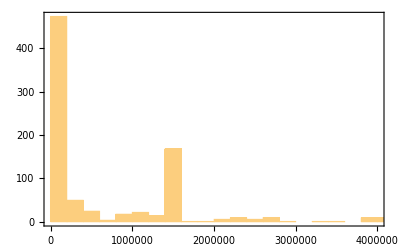

```mathematica
Histogram[areas,Frame->True]
```

```mathematica
mn=Min[areas]
```

352.76

```mathematica
mx=Max[areas]
```

6.56699×10^7

```mathematica
grays=1-(#-mn)/(mx-mn)&/@areas;
```

```mathematica
grays;
```

## render

```mathematica
Polygon[pFaces[[3]]]
Graphics3D[%]
```

```mathematica
polys=Polygon[#]&/@pFaces;
```

```mathematica
Dimensions[polys]
```

{901}

```mathematica
z={polys,grays}ᵀ ;
```

```mathematica
tbl=Graphics3D[{GrayLevel[#[[2]]],#[[1]]}]&/@z;
```

```mathematica
Show[tbl]
```

```mathematica
Graphics3D[polys]
```

## end

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```